```mathematica
(*Algorithm:LM-STLS (Levenberg-Marquardt Sequential Thresholded Least Squares)
Reference to cite when using this code:[1] A noise-corrected data-driven approach for nonlinear dynamical system modeling in frequency domain,2026.
Code availability:This program is open for academic research only.Unauthorized commercial redistribution is prohibited.
================================================================================*)
```

```mathematica
(*Import self-defined package for nonlinear sparse identification*)
Import["NCSINDyPackage.m","Package"]
```

```mathematica
(* ======================Basic System Configuration======================*)
(*n:nonlinear polynomial order;order:Fourier series expansion order*)
n=7;order=5;opts={AccuracyGoal->12,PrecisionGoal->12,MaxStepFraction->1/1000 };
(*Governing differential equation of nonlinear oscillator*)
Eq01={m x''[t]+c x'[t]+∑_(j1=1)^n Subscript[k, j1] x[t]^j1-F Cos[Ω t]==0};
(*Initial conditions of dynamic system*)
InitCond01={x[0]==0, x'[0]==0};
(*True physical parameter values for simulation*)
Par01=Join[{m->1,c->0.05,F->1},Thread[Table[Subscript[k, j1],{j1,1,n}]->{1,0.4,0.5,0,0.2,0,0}]];
(*List of undetermined physical coefficients to be identified*)
Var=Join[{m,c},Table[Subscript[k, j1],{j1,1,n}]];
```

```mathematica
(* ======================Fourier Series Model Definition======================*)
(*Displacement,velocity,acceleration Fourier series model*)
(*DispModel:displacement Fourier approximation*)
DispModel=Subscript[A, s,0]+∑_(j1=1)^order (Subscript[A, s,j1] Cos[j1 Ω t]+Subscript[B, s,j1] Sin[j1 Ω t]);
(*Coefficient list for displacement Fourier series*)
DispCoeff=Join[{Subscript[A, s,0]},Flatten[Table[{Subscript[A, s,j1],Subscript[B, s,j1]},{j1,order}]]];
(*VeloModel:velocity Fourier approximation*)
VeloModel=Subscript[A, v,0]+∑_(j1=1)^order (Subscript[A, v,j1] Cos[j1 Ω t]+Subscript[B, v,j1] Sin[j1 Ω t]);VeloCoeff=Join[{Subscript[A, v,0]},Flatten[Table[{Subscript[A, v,j1],Subscript[B, v,j1]},{j1,order}]]];
(*AcceModel:acceleration Fourier approximation*)
AcceModel=Subscript[A, a,0]+∑_(j1=1)^order (Subscript[A, a,j1] Cos[j1 Ω t]+Subscript[B, a,j1] Sin[j1 Ω t]);AcceCoeff=Join[{Subscript[A, a,0]},Flatten[Table[{Subscript[A, a,j1],Subscript[B, a,j1]},{j1,order}]]];
(*Harmonic orders used for noise correction*)
OrderCorrect={4,5};
(*Coefficient set of noise correction terms*)
CorrectModel=Sum[Subscript[δA, a,j1] Cos[j1 Ω t]+Subscript[δB, a,j1] Sin[j1 Ω t],{j1,OrderCorrect}];
(*Coefficient set of noise correction terms*)
CorrectCoeff=DeleteCases[Flatten[Table[{Subscript[δA, a,j1],Subscript[δB, a,j1]},{j1,OrderCorrect}]],Subscript[δB, a,0]];
(*Sub-function:construct correction coefficients for each excitation frequency*)
CorrectCoeffj[jj_]:=Join[{Subscript[δA, a,0][jj]},Flatten[Table[{Subscript[δA, a,j1][jj],Subscript[δB, a,j1][jj]},{j1,order}]]]/.Subscript[x1_, x2_,x3_][x4_]/;MemberQ[Complement[Range[0,order],OrderCorrect],x3]->0;
(*Extract variable symbols of noise correction coefficients*)
CorrectCoeffjVar[jj_]:=DeleteCases[Flatten[Table[{Subscript[δA, a,j1][jj],Subscript[δB, a,j1][jj]},{j1,OrderCorrect}]],Subscript[δB, a,0][jj]];
```

```mathematica
(*Nonlinear stiffness model library constructed from displacement harmonics*)
StiffnessModel=ModelLibFun[{DispCoeff},n,order];
(*Excitation frequency list for sweeping analysis*)
OmegaList=Range[0.5,4,0.5];
(*Sampling time sequence*)TimeData=Range[800,1000,0.01];
(*Signal-to-Noise Ratio*)
SNR=10;
```

```mathematica
(*Load preset noise data from external file for reproducibility*)
Noise=Transpose[Import["C:/Users/Administrator/Desktop/Noise42.xls"][[1]]];
```

```mathematica
(* ======================Generate Dynamic Response Data======================*)
For[j2=1,j2≤Length[OmegaList],j2++,
(*Solve ODE to obtain true displacement response*)
Sol01[j2]=NDSolveValue[Join[Eq01,InitCond01]/.Par01/.Ω->OmegaList[[j2]],x,{t,0,1000},opts];
(*True acceleration time series data*)
AcceData[j2]=Array[{TimeData[[#]],Sol01[j2]''[TimeData[[#]]]}&,Length[TimeData]];
AcceSigTrue[j2]=Array[Sol01[j2]''[TimeData[[#]]]&,Length[TimeData]];
(*Add preset noise to obtain measured noisy acceleration*)
(*AcceSigNois[j2]=AddNoiseFun[AcceSigTrue[j2],0,10];*)
AcceSigNois[j2]=Noise[[j2]];
(*AcceSigNois[j2]=Noise[[j2]];*)
AcceDataMeas[j2]=Array[{TimeData[[#]],AcceSigTrue[j2][[#]]+AcceSigNois[j2][[#]]}&,Length[TimeData]];
(* ======================Fourier Coefficient Identification via Fitting======================*)(*Fourier coefficients fitted from noisy measured data*)
Ameas[x''][j2]=AcceCoeff/.FindFit[AcceDataMeas[j2],AcceModel/.Par01/.Ω->OmegaList[[j2]],AcceCoeff,t];
(*Fourier coefficients fitted from noise-free true data*)
Atrue[x''][j2]=AcceCoeff/.FindFit[AcceData[j2],AcceModel/.Par01/.Ω->OmegaList[[j2]],AcceCoeff,t];
(*Fourier coefficients of pure noise component*)
Anois[x''][j2]=CorrectCoeff/.FindFit[Array[{TimeData[[#]],AcceSigNois[j2][[#]]}&,Length[TimeData]],CorrectModel/.Par01/.Ω->OmegaList[[j2]],CorrectCoeff,t];
(*Noise correction for acceleration harmonic coefficients*)
A[x''][j2]=ReplacePart[Ameas[x''][j2]-(CorrectCoeffj[j2]/.Ω->OmegaList[[j2]]),1->0];
(* ======================Full-State Reconstruction via SVA Transform======================*)(*Reconstruct velocity and acceleration from corrected displacement harmonics*)
A[x][j2]=ReplacePart[SVATransform[A[x''][j2],"rad/s",OmegaList[[j2]],"a2s"],1->Subscript[δA, s,0][j2]];
A[x'][j2]=ReplacePart[SVATransform[A[x''][j2],"rad/s",OmegaList[[j2]],"a2v"],1->0];
(*Excitation force harmonic coefficients*)
A[f][j2]=Join[{0,F},Table[0,2order-1]]/.Par01;
(*Construct nonlinear library matrix in frequency domain*)
ModelLibrary[j2]=StiffnessModel/.Thread[DispCoeff->A[x][j2]];
(*Assemble Jacobian-like matrix and residual vector for nonlinear least squares*)
AA1[j2]=Join[{A[x''][j2]}ᵀ,{A[x'][j2]}ᵀ,ModelLibrary[j2],2].{Var}ᵀ//Chop;
RR1[j2]=Flatten[AA1[j2]-{A[f][j2]}ᵀ];
Print[j2/Length[OmegaList]//N];
]
```

0.125

0.25

0.375

0.5

0.625

0.75

0.875

1.

```mathematica
(* ======================Prepare Training Data for Sparse Regression======================*)(*Collect noisy and noise-free training time-series data*)
TrainDataAcceMeas=Table[AcceDataMeas[j1],{j1,1,Length[OmegaList]}];TrainDataAcceTrue=Table[AcceData[j1],{j1,1,Length[OmegaList]}];
(*Plot noisy and true acceleration responses*)
Fig2aNoise=ListLinePlot[Flatten[Table[AcceDataMeas[j1][[All,2]],{j1,1,Length[OmegaList]}]],PlotStyle->{Red,Dotted},Frame->True,PlotRange->All];
Fig2aTrue=ListLinePlot[Flatten[Table[AcceData[j1][[All,2]],{j1,1,Length[OmegaList]}]],PlotStyle->{Blue},Frame->True,PlotRange->All];
Fig2a=Show[Fig2aNoise,Fig2aTrue,PlotRange->All]
```

-Graphics-

```mathematica
(* ======================LM-STLS Algorithm Hyperparameters======================*)
ConvTol=10^-6;maxLMIter=100;
Lambda=0.06;maxSparseIter=10;
(*Combine residual across all excitation frequencies*)
Residual=Join@@Table[RR1[j2],{j2,1,Length[OmegaList]}];
```

```mathematica
(*Case1：the streaming corruption is not corrected, the damping is not protected, Lambda is too large*)
(*Combine residual across all excitation frequencies*)
Residual01=Residual/.Thread[Table[Subscript[δA, s,0][j2],{j2,1,Length[OmegaList]}]->0];
(*Merge physical parameters and noise correction coefficients into full variable set*)
Variable01=Join[Var,Table[Join[CorrectCoeffjVar[j2]],{j2,1,Length[OmegaList]}]//Flatten];
(*Compute Jacobian matrix of residual with respect to unknown variables*)
JacobiFun01=D[Residual01,{Variable01,1}];
(*Initial guess of unknown parameter vector*)
InitGuess01=ReplacePart[ReplacePart[0.2*Variable01/.Par01,Thread[Range[Length[Var]+1,Length[Variable01]]->0]],Thread[{6,8,9}->1]];
(*Indices of physical terms forced to be retained during thresholding*)
InitbigIndices01=Join[Range[Length[Var]+1,Length[Variable01]]];
```

```mathematica
(*Execute proposed LM-STLS nonlinear sparse regression*)
Xi01=NonLinearSparsifyDynamics[JacobiFun01,Residual01,Variable01,InitGuess01,ConvTol,maxLMIter,Lambda,maxSparseIter,InitbigIndices01];
```

{1,38}

{2,37}

{3,37}

{4,37}

{5,37}

{6,37}

{7,37}

{8,37}

{9,37}

{10,37}

```mathematica
(*Case 1: Show iterative evolution of parameter identification for {m,c,Subscript[k, 1],Subscript[k, 2],Subscript[k, 3],Subscript[k, 4],Subscript[k, 5],Subscript[k, 6],Subscript[k, 7]}*)
Xi01[[1]]//MatrixForm
```

(0.2 | 0.01 | 0.2 | 0.08 | 0.1 | 1. | 0.04 | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.986572 | 0.0499218 | 0.941668 | -0.0490625 | 0.47118 | 0.159168 | 0.174376 | -0.0558049 | 0.0179488 | 0.0514614 | -0.0115341 | 0.148608 | -0.0219736 | -0.00602076 | 0.00677006 | -0.0563409 | -0.0307212 | 0.0310932 | 0.021234 | -0.104005 | -0.0899831 | -0.0126993 | 0.00142084 | 0.0189923 | 0.00241516 | 0.00176572 | 0.00736374 | -0.00716546 | 0.0212587 | -0.0115267 | -0.0212315 | -0.00217555 | 0.0156753 | -0.0105999 | 0.000797134 | 0.000205426 | 0.00166115 | -0.00879357 | 0.010921 | 0.00924826 | 0.0238245
0.987976 | 0.0506204 | 0.937056 | 0.0390145 | 0.760642 | 0.0595134 | -0.138694 | -0.0300364 | 0.0934037 | 0.0451694 | 0.00986218 | -0.0337469 | -0.00203435 | 0.0318179 | 0.012043 | -0.0168506 | -0.00705113 | 0.0309796 | 0.0265542 | 0.0706409 | 0.0490711 | -0.00341672 | 0.000389212 | 0.00495148 | 0.000594327 | 0.000438942 | 0.00189018 | -0.00182356 | 0.00543395 | -0.00294713 | -0.00542487 | -0.000554248 | 0.00400166 | -0.00270652 | 0.00020341 | 0.0000525693 | 0.000423857 | -0.00224426 | 0.00278795 | 0.00236016 | 0.00607792
0.9819 | 0.0506479 | 0.886296 | 0.0710201 | 0.930536 | 0.0224854 | -0.284573 | -0.0204158 | 0.126102 | 0.0245795 | 0.00991809 | -0.0315507 | -0.00143826 | 0.0255358 | 0.0106746 | -0.0305754 | -0.0110951 | 0.032418 | 0.0273284 | 0.0780051 | 0.0541247 | -0.0034392 | 0.000387175 | 0.00495409 | 0.000583705 | 0.000431307 | 0.0018803 | -0.00181052 | 0.00540157 | -0.00293059 | -0.00539267 | -0.000551602 | 0.00397689 | -0.00269147 | 0.000202352 | 0.0000520563 | 0.000421341 | -0.00223162 | 0.00277173 | 0.00234577 | 0.006043
0.979522 | 0.0506518 | 0.865465 | 0.059712 | 1.01797 | 0.0374978 | -0.364845 | -0.0245804 | 0.144809 | 0.026502 | 0.0094927 | -0.0340309 | -0.00185342 | 0.0271601 | 0.0110965 | -0.037549 | -0.0131487 | 0.0308041 | 0.0265052 | 0.0837667 | 0.0580385 | -0.00341022 | 0.000379253 | 0.00497644 | 0.000579648 | 0.000435098 | 0.00188003 | -0.0018091 | 0.00540135 | -0.00292994 | -0.0053925 | -0.000551288 | 0.00397671 | -0.00269129 | 0.00020242 | 0.0000521356 | 0.000421277 | -0.00223152 | 0.00277161 | 0.00234568 | 0.00604275
0.979248 | 0.0506497 | 0.863171 | 0.0614662 | 1.02456 | 0.0354182 | -0.370068 | -0.0240301 | 0.145921 | 0.0243239 | 0.0093915 | -0.033105 | -0.00186427 | 0.0270116 | 0.0110652 | -0.0381103 | -0.0133167 | 0.0309085 | 0.0265623 | 0.0838422 | 0.0580772 | -0.00341231 | 0.000378798 | 0.00497834 | 0.000579313 | 0.000435057 | 0.00188012 | -0.00180898 | 0.00540138 | -0.00292993 | -0.00539249 | -0.00055124 | 0.00397672 | -0.00269129 | 0.000202415 | 0.0000521519 | 0.000421266 | -0.00223152 | 0.00277161 | 0.00234568 | 0.00604275
0.979161 | 0.0506501 | 0.862391 | 0.0603555 | 1.02845 | 0.0368459 | -0.373813 | -0.0244205 | 0.146817 | 0.0246547 | 0.00938023 | -0.0333367 | -0.00188881 | 0.0271883 | 0.0111078 | -0.0384187 | -0.0134076 | 0.030776 | 0.0264946 | 0.0841823 | 0.0583095 | -0.00340977 | 0.000378267 | 0.00497938 | 0.000579133 | 0.000435356 | 0.0018801 | -0.00180892 | 0.00540138 | -0.00292988 | -0.0053925 | -0.000551227 | 0.00397672 | -0.00269127 | 0.000202416 | 0.0000521555 | 0.000421264 | -0.00223152 | 0.00277161 | 0.00234568 | 0.00604275
0.979173 | 0.0506499 | 0.862503 | 0.0606675 | 1.02776 | 0.0364503 | -0.373124 | -0.0243127 | 0.146649 | 0.0244682 | 0.00937885 | -0.0332395 | -0.00188318 | 0.0271486 | 0.0110983 | -0.0383666 | -0.0133925 | 0.0308111 | 0.0265128 | 0.0841107 | 0.05826 | -0.0034104 | 0.000378354 | 0.00497921 | 0.000579162 | 0.000435293 | 0.00188011 | -0.00180893 | 0.00540139 | -0.00292989 | -0.0053925 | -0.000551227 | 0.00397672 | -0.00269128 | 0.000202415 | 0.0000521556 | 0.000421264 | -0.00223152 | 0.00277161 | 0.00234568 | 0.00604275
0.979166 | 0.05065 | 0.862441 | 0.0605413 | 1.0281 | 0.0366113 | -0.373461 | -0.0243566 | 0.14673 | 0.024527 | 0.00937856 | -0.0332732 | -0.00188558 | 0.0271663 | 0.0111026 | -0.0383932 | -0.0134003 | 0.0307965 | 0.0265053 | 0.0841436 | 0.0582826 | -0.00341013 | 0.000378309 | 0.0049793 | 0.000579147 | 0.000435322 | 0.00188011 | -0.00180893 | 0.00540139 | -0.00292989 | -0.0053925 | -0.000551227 | 0.00397672 | -0.00269128 | 0.000202416 | 0.0000521557 | 0.000421264 | -0.00223152 | 0.00277161 | 0.00234568 | 0.00604275
0.979169 | 0.0506499 | 0.862461 | 0.0605855 | 1.02799 | 0.0365549 | -0.37335 | -0.0243413 | 0.146703 | 0.0245045 | 0.00937857 | -0.0332607 | -0.00188475 | 0.0271603 | 0.0111011 | -0.0383845 | -0.0133977 | 0.0308016 | 0.0265079 | 0.0841325 | 0.058275 | -0.00341022 | 0.000378324 | 0.00497927 | 0.000579152 | 0.000435312 | 0.00188011 | -0.00180893 | 0.00540139 | -0.00292989 | -0.0053925 | -0.000551227 | 0.00397672 | -0.00269128 | 0.000202416 | 0.0000521557 | 0.000421264 | -0.00223152 | 0.00277161 | 0.00234568 | 0.00604275
0.979168 | 0.0506499 | 0.862453 | 0.0605692 | 1.02803 | 0.0365757 | -0.373392 | -0.0243469 | 0.146713 | 0.0245125 | 0.00937855 | -0.0332652 | -0.00188506 | 0.0271625 | 0.0111017 | -0.0383878 | -0.0133987 | 0.0307997 | 0.0265069 | 0.0841367 | 0.0582779 | -0.00341019 | 0.000378318 | 0.00497928 | 0.00057915 | 0.000435316 | 0.00188011 | -0.00180893 | 0.00540139 | -0.00292989 | -0.0053925 | -0.000551227 | 0.00397672 | -0.00269128 | 0.000202416 | 0.0000521557 | 0.000421264 | -0.00223152 | 0.00277161 | 0.00234568 | 0.00604275
0.979168 | 0.0506499 | 0.862456 | 0.0605751 | 1.02802 | 0.0365682 | -0.373377 | -0.0243449 | 0.14671 | 0.0245096 | 0.00937856 | -0.0332636 | -0.00188495 | 0.0271617 | 0.0111015 | -0.0383866 | -0.0133983 | 0.0308004 | 0.0265073 | 0.0841352 | 0.0582768 | -0.0034102 | 0.00037832 | 0.00497928 | 0.000579151 | 0.000435314 | 0.00188011 | -0.00180893 | 0.00540139 | -0.00292989 | -0.0053925 | -0.000551227 | 0.00397672 | -0.00269128 | 0.000202416 | 0.0000521557 | 0.000421264 | -0.00223152 | 0.00277161 | 0.00234568 | 0.00604275
0.979168 | 0.0506499 | 0.862455 | 0.0605729 | 1.02802 | 0.0365709 | -0.373382 | -0.0243456 | 0.146711 | 0.0245106 | 0.00937856 | -0.0332642 | -0.00188499 | 0.027162 | 0.0111015 | -0.0383871 | -0.0133985 | 0.0308001 | 0.0265071 | 0.0841357 | 0.0582772 | -0.0034102 | 0.00037832 | 0.00497928 | 0.000579151 | 0.000435315 | 0.00188011 | -0.00180893 | 0.00540139 | -0.00292989 | -0.0053925 | -0.000551227 | 0.00397672 | -0.00269128 | 0.000202416 | 0.0000521557 | 0.000421264 | -0.00223152 | 0.00277161 | 0.00234568 | 0.00604275
0.979168 | 0.0506499 | 0.862455 | 0.0605737 | 1.02802 | 0.0365699 | -0.37338 | -0.0243454 | 0.146711 | 0.0245102 | 0.00937856 | -0.0332639 | -0.00188498 | 0.0271619 | 0.0111015 | -0.0383869 | -0.0133984 | 0.0308002 | 0.0265072 | 0.0841355 | 0.0582771 | -0.0034102 | 0.00037832 | 0.00497928 | 0.000579151 | 0.000435315 | 0.00188011 | -0.00180893 | 0.00540139 | -0.00292989 | -0.0053925 | -0.000551227 | 0.00397672 | -0.00269128 | 0.000202416 | 0.0000521557 | 0.000421264 | -0.00223152 | 0.00277161 | 0.00234568 | 0.00604275
0.979168 | 0.0506499 | 0.862455 | 0.0605734 | 1.02802 | 0.0365703 | -0.373381 | -0.0243455 | 0.146711 | 0.0245104 | 0.00937856 | -0.033264 | -0.00188498 | 0.0271619 | 0.0111015 | -0.038387 | -0.0133984 | 0.0308002 | 0.0265072 | 0.0841356 | 0.0582771 | -0.0034102 | 0.00037832 | 0.00497928 | 0.000579151 | 0.000435315 | 0.00188011 | -0.00180893 | 0.00540139 | -0.00292989 | -0.0053925 | -0.000551227 | 0.00397672 | -0.00269128 | 0.000202416 | 0.0000521557 | 0.000421264 | -0.00223152 | 0.00277161 | 0.00234568 | 0.00604275
0.979168 | 0 | 0.862455 | 0.0605736 | 1.02802 | 0 | -0.373381 | 0 | 0.146711 | 0.0245103 | 0.00937856 | -0.033264 | -0.00188498 | 0.0271619 | 0.0111015 | -0.0383869 | -0.0133984 | 0.0308002 | 0.0265072 | 0.0841356 | 0.0582771 | -0.0034102 | 0.00037832 | 0.00497928 | 0.000579151 | 0.000435315 | 0.00188011 | -0.00180893 | 0.00540139 | -0.00292989 | -0.0053925 | -0.000551227 | 0.00397672 | -0.00269128 | 0.000202416 | 0.0000521557 | 0.000421264 | -0.00223152 | 0.00277161 | 0.00234568 | 0.00604275
0.979283 | 0 | 0.868788 | 0.0218083 | 1.00178 | 0 | -0.35527 | 0 | 0.143314 | 0.0239788 | 0.0106064 | -0.0352271 | -0.00182272 | 0.0353856 | 0.0129858 | -0.0344552 | -0.0122982 | 0.0905077 | 0.0574966 | 0.0862489 | 0.0599242 | -0.00346472 | 0.00038733 | 0.00497481 | 0.000579666 | 0.000429163 | 0.00188107 | -0.00180916 | 0.00540139 | -0.00293061 | -0.00539235 | -0.000551282 | 0.00397672 | -0.00269134 | 0.000202259 | 0.0000521396 | 0.000421272 | -0.00223157 | 0.00277162 | 0.00234567 | 0.00604275
0.980725 | 0 | 0.881025 | 0.0216211 | 0.954009 | 0 | -0.312225 | 0 | 0.133377 | 0.0252397 | 0.0117893 | -0.0356102 | -0.00174334 | 0.0355701 | 0.0130541 | -0.0307029 | -0.0111712 | 0.0912848 | 0.0579789 | 0.0834061 | 0.0579368 | -0.00346678 | 0.000389221 | 0.00496285 | 0.000581801 | 0.000428605 | 0.00188122 | -0.00180988 | 0.00540141 | -0.00293045 | -0.00539231 | -0.000551421 | 0.00397672 | -0.00269122 | 0.000202141 | 0.000052103 | 0.00042129 | -0.00223155 | 0.00277162 | 0.00234567 | 0.00604275
0.982009 | 0 | 0.89201 | 0.021535 | 0.911984 | 0 | -0.274799 | 0 | 0.124803 | 0.0256404 | 0.0120595 | -0.0353395 | -0.00157615 | 0.03582 | 0.0130827 | -0.0273848 | -0.0102038 | 0.091295 | 0.0579843 | 0.0811967 | 0.0564472 | -0.0034693 | 0.000391105 | 0.00495241 | 0.000583705 | 0.000428021 | 0.00188118 | -0.0018105 | 0.00540141 | -0.00293051 | -0.0053923 | -0.00055155 | 0.00397672 | -0.00269121 | 0.000202117 | 0.0000520676 | 0.000421309 | -0.00223154 | 0.00277162 | 0.00234566 | 0.00604275
0.982467 | 0 | 0.895927 | 0.0215032 | 0.897352 | 0 | -0.261872 | 0 | 0.121855 | 0.0262645 | 0.0121716 | -0.035462 | -0.00152772 | 0.0358833 | 0.0130846 | -0.0262205 | -0.00988835 | 0.0913567 | 0.0580183 | 0.0804713 | 0.0559755 | -0.00347043 | 0.000391972 | 0.00494875 | 0.000584402 | 0.000427754 | 0.00188117 | -0.00181072 | 0.0054014 | -0.00293053 | -0.0053923 | -0.000551604 | 0.00397671 | -0.00269121 | 0.000202105 | 0.0000520521 | 0.000421318 | -0.00223154 | 0.00277162 | 0.00234566 | 0.00604275
0.982542 | 0 | 0.896569 | 0.0214953 | 0.894873 | 0 | -0.259647 | 0 | 0.121342 | 0.0264656 | 0.0121909 | -0.035514 | -0.00151918 | 0.0358885 | 0.0130829 | -0.0260163 | -0.00983994 | 0.091384 | 0.0580334 | 0.0803286 | 0.0558861 | -0.0034707 | 0.000392181 | 0.0049481 | 0.000584535 | 0.000427689 | 0.00188116 | -0.00181076 | 0.0054014 | -0.00293054 | -0.0053923 | -0.000551616 | 0.00397671 | -0.00269121 | 0.000202103 | 0.0000520484 | 0.00042132 | -0.00223153 | 0.00277162 | 0.00234566 | 0.00604275
0.982551 | 0 | 0.896652 | 0.0214938 | 0.894526 | 0 | -0.259325 | 0 | 0.121267 | 0.0264975 | 0.0121938 | -0.0355197 | -0.0015183 | 0.0358892 | 0.0130826 | -0.0259868 | -0.00983334 | 0.091389 | 0.0580361 | 0.0803034 | 0.0558704 | -0.00347074 | 0.000392214 | 0.004948 | 0.000584554 | 0.000427679 | 0.00188116 | -0.00181077 | 0.0054014 | -0.00293054 | -0.0053923 | -0.000551617 | 0.00397671 | -0.00269121 | 0.000202102 | 0.0000520479 | 0.00042132 | -0.00223153 | 0.00277162 | 0.00234566 | 0.00604275
0.982553 | 0 | 0.896661 | 0.0214936 | 0.894483 | 0 | -0.259286 | 0 | 0.121257 | 0.0265029 | 0.0121942 | -0.0355207 | -0.00151829 | 0.0358892 | 0.0130825 | -0.0259831 | -0.00983257 | 0.0913898 | 0.0580366 | 0.0803001 | 0.0558684 | -0.00347075 | 0.000392218 | 0.00494799 | 0.000584557 | 0.000427678 | 0.00188116 | -0.00181077 | 0.0054014 | -0.00293054 | -0.0053923 | -0.000551618 | 0.00397671 | -0.00269121 | 0.000202102 | 0.0000520478 | 0.00042132 | -0.00223153 | 0.00277162 | 0.00234566 | 0.00604275
0.982553 | 0 | 0.896663 | 0.0214935 | 0.894477 | 0 | -0.25928 | 0 | 0.121256 | 0.0265035 | 0.0121943 | -0.0355207 | -0.00151828 | 0.0358893 | 0.0130825 | -0.0259826 | -0.00983243 | 0.0913899 | 0.0580366 | 0.0802995 | 0.055868 | -0.00347075 | 0.000392219 | 0.00494799 | 0.000584557 | 0.000427677 | 0.00188116 | -0.00181077 | 0.0054014 | -0.00293054 | -0.0053923 | -0.000551618 | 0.00397671 | -0.00269121 | 0.000202102 | 0.0000520478 | 0.00042132 | -0.00223153 | 0.00277162 | 0.00234566 | 0.00604275
0.982553 | 0 | 0.896663 | 0 | 0.894476 | 0 | -0.259279 | 0 | 0.121256 | 0.0265037 | 0.0121943 | -0.0355207 | -0.00151828 | 0.0358893 | 0.0130825 | -0.0259825 | -0.00983242 | 0.0913899 | 0.0580366 | 0.0802995 | 0.055868 | -0.00347075 | 0.000392219 | 0.00494799 | 0.000584557 | 0.000427677 | 0.00188116 | -0.00181077 | 0.0054014 | -0.00293054 | -0.0053923 | -0.000551618 | 0.00397671 | -0.00269121 | 0.000202102 | 0.0000520478 | 0.00042132 | -0.00223153 | 0.00277162 | 0.00234566 | 0.00604275
0.98251 | 0 | 0.89889 | 0 | 0.88552 | 0 | -0.253505 | 0 | 0.120295 | 0.0285696 | 0.0131906 | -0.0369788 | -0.00166867 | 0.0359053 | 0.013152 | -0.0252384 | -0.00960122 | 0.0937737 | 0.0594215 | 0.0813737 | 0.0566343 | -0.00347018 | 0.000392465 | 0.00494643 | 0.000584829 | 0.000427685 | 0.00188144 | -0.00181086 | 0.0054014 | -0.00293021 | -0.00539225 | -0.000551637 | 0.00397671 | -0.00269102 | 0.000201958 | 0.0000520425 | 0.000421323 | -0.00223151 | 0.00277162 | 0.00234566 | 0.00604275
0.982926 | 0 | 0.902467 | 0 | 0.871305 | 0 | -0.240681 | 0 | 0.117336 | 0.0282671 | 0.0132485 | -0.0367325 | -0.00157886 | 0.0360027 | 0.0131661 | -0.024115 | -0.00926588 | 0.0937648 | 0.0594175 | 0.0805848 | 0.0560747 | -0.00347097 | 0.000393044 | 0.00494291 | 0.00058546 | 0.000427506 | 0.00188143 | -0.00181107 | 0.0054014 | -0.00293022 | -0.00539225 | -0.000551678 | 0.00397671 | -0.00269102 | 0.00020195 | 0.0000520315 | 0.000421328 | -0.0022315 | 0.00277162 | 0.00234566 | 0.00604275
0.983291 | 0 | 0.90558 | 0 | 0.859641 | 0 | -0.230376 | 0 | 0.114986 | 0.0284509 | 0.0133289 | -0.0367133 | -0.0015402 | 0.0360766 | 0.013175 | -0.0231999 | -0.00899999 | 0.0937318 | 0.0593996 | 0.080012 | 0.0556901 | -0.00347172 | 0.000393578 | 0.00494006 | 0.000585981 | 0.000427339 | 0.00188142 | -0.00181124 | 0.00540141 | -0.00293024 | -0.00539224 | -0.000551714 | 0.00397671 | -0.00269102 | 0.000201943 | 0.0000520217 | 0.000421334 | -0.0022315 | 0.00277162 | 0.00234566 | 0.00604275
0.98342 | 0 | 0.906682 | 0 | 0.855499 | 0 | -0.226706 | 0 | 0.114148 | 0.0286176 | 0.0133567 | -0.0367481 | -0.00152565 | 0.0361011 | 0.0131771 | -0.0228701 | -0.00891031 | 0.0937205 | 0.0593938 | 0.0798017 | 0.0555524 | -0.00347206 | 0.000393825 | 0.00493903 | 0.000586177 | 0.000427262 | 0.00188142 | -0.00181131 | 0.0054014 | -0.00293025 | -0.00539224 | -0.000551729 | 0.00397671 | -0.00269102 | 0.00020194 | 0.0000520173 | 0.000421336 | -0.0022315 | 0.00277162 | 0.00234566 | 0.00604275
0.983441 | 0 | 0.906863 | 0 | 0.854804 | 0 | -0.226083 | 0 | 0.114004 | 0.0286801 | 0.0133617 | -0.0367661 | -0.00152346 | 0.0361049 | 0.0131771 | -0.0228127 | -0.00889676 | 0.0937187 | 0.0593929 | 0.0797618 | 0.0555275 | -0.00347214 | 0.000393885 | 0.00493885 | 0.000586214 | 0.000427244 | 0.00188141 | -0.00181132 | 0.0054014 | -0.00293025 | -0.00539224 | -0.000551733 | 0.00397671 | -0.00269102 | 0.00020194 | 0.0000520163 | 0.000421337 | -0.0022315 | 0.00277162 | 0.00234566 | 0.00604275
0.983444 | 0 | 0.906888 | 0 | 0.854696 | 0 | -0.225982 | 0 | 0.113981 | 0.0286888 | 0.0133624 | -0.0367674 | -0.00152317 | 0.0361056 | 0.0131771 | -0.0228036 | -0.00889463 | 0.0937184 | 0.0593928 | 0.0797537 | 0.0555223 | -0.00347215 | 0.000393894 | 0.00493882 | 0.00058622 | 0.000427241 | 0.00188141 | -0.00181132 | 0.0054014 | -0.00293025 | -0.00539224 | -0.000551733 | 0.00397671 | -0.00269102 | 0.000201939 | 0.0000520161 | 0.000421337 | -0.0022315 | 0.00277162 | 0.00234566 | 0.00604275
0.983444 | 0 | 0.906891 | 0 | 0.854684 | 0 | -0.225971 | 0 | 0.113978 | 0.0286908 | 0.0133625 | -0.0367679 | -0.00152319 | 0.0361056 | 0.0131771 | -0.0228025 | -0.00889444 | 0.0937184 | 0.0593928 | 0.0797528 | 0.0555218 | -0.00347215 | 0.000393896 | 0.00493881 | 0.000586221 | 0.00042724 | 0.00188141 | -0.00181132 | 0.0054014 | -0.00293025 | -0.00539224 | -0.000551733 | 0.00397671 | -0.00269102 | 0.000201939 | 0.0000520161 | 0.000421337 | -0.0022315 | 0.00277162 | 0.00234566 | 0.00604275
0.983444 | 0 | 0.906892 | 0 | 0.854682 | 0 | -0.225968 | 0 | 0.113977 | 0.0286909 | 0.0133626 | -0.0367679 | -0.00152318 | 0.0361057 | 0.0131771 | -0.0228023 | -0.00889438 | 0.0937184 | 0.0593928 | 0.0797526 | 0.0555217 | -0.00347215 | 0.000393896 | 0.00493881 | 0.000586221 | 0.00042724 | 0.00188141 | -0.00181132 | 0.0054014 | -0.00293025 | -0.00539224 | -0.000551733 | 0.00397671 | -0.00269102 | 0.000201939 | 0.0000520161 | 0.000421337 | -0.0022315 | 0.00277162 | 0.00234566 | 0.00604275
0.983444 | 0 | 0.906892 | 0 | 0.854681 | 0 | -0.225968 | 0 | 0.113977 | 0.028691 | 0.0133626 | -0.0367679 | -0.00152318 | 0.0361057 | 0.0131771 | -0.0228023 | -0.00889438 | 0.0937184 | 0.0593928 | 0.0797526 | 0.0555217 | -0.00347215 | 0.000393896 | 0.00493881 | 0.000586221 | 0.00042724 | 0.00188141 | -0.00181132 | 0.0054014 | -0.00293025 | -0.00539224 | -0.000551733 | 0.00397671 | -0.00269102 | 0.000201939 | 0.0000520161 | 0.000421337 | -0.0022315 | 0.00277162 | 0.00234566 | 0.00604275
0.983444 | 0 | 0.906892 | 0 | 0.854681 | 0 | -0.225968 | 0 | 0.113977 | 0.028691 | 0.0133626 | -0.0367679 | -0.00152318 | 0.0361057 | 0.0131771 | -0.0228023 | -0.00889438 | 0.0937184 | 0.0593928 | 0.0797526 | 0.0555217 | -0.00347215 | 0.000393896 | 0.00493881 | 0.000586221 | 0.00042724 | 0.00188141 | -0.00181132 | 0.0054014 | -0.00293025 | -0.00539224 | -0.000551733 | 0.00397671 | -0.00269102 | 0.000201939 | 0.0000520161 | 0.000421337 | -0.0022315 | 0.00277162 | 0.00234566 | 0.00604275
0.983444 | 0 | 0.906892 | 0 | 0.854681 | 0 | -0.225968 | 0 | 0.113977 | 0.028691 | 0.0133626 | -0.0367679 | -0.00152318 | 0.0361057 | 0.0131771 | -0.0228023 | -0.00889438 | 0.0937184 | 0.0593928 | 0.0797526 | 0.0555217 | -0.00347215 | 0.000393896 | 0.00493881 | 0.000586221 | 0.00042724 | 0.00188141 | -0.00181132 | 0.0054014 | -0.00293025 | -0.00539224 | -0.000551733 | 0.00397671 | -0.00269102 | 0.000201939 | 0.0000520161 | 0.000421337 | -0.0022315 | 0.00277162 | 0.00234566 | 0.00604275
0.983444 | 0 | 0.906892 | 0 | 0.854681 | 0 | -0.225968 | 0 | 0.113977 | 0.028691 | 0.0133626 | -0.0367679 | -0.00152318 | 0.0361057 | 0.0131771 | -0.0228023 | -0.00889438 | 0.0937184 | 0.0593928 | 0.0797526 | 0.0555217 | -0.00347215 | 0.000393896 | 0.00493881 | 0.000586221 | 0.00042724 | 0.00188141 | -0.00181132 | 0.0054014 | -0.00293025 | -0.00539224 | -0.000551733 | 0.00397671 | -0.00269102 | 0.000201939 | 0.0000520161 | 0.000421337 | -0.0022315 | 0.00277162 | 0.00234566 | 0.00604275
0.983444 | 0 | 0.906892 | 0 | 0.854681 | 0 | -0.225968 | 0 | 0.113977 | 0.028691 | 0.0133626 | -0.0367679 | -0.00152318 | 0.0361057 | 0.0131771 | -0.0228023 | -0.00889438 | 0.0937184 | 0.0593928 | 0.0797526 | 0.0555217 | -0.00347215 | 0.000393896 | 0.00493881 | 0.000586221 | 0.00042724 | 0.00188141 | -0.00181132 | 0.0054014 | -0.00293025 | -0.00539224 | -0.000551733 | 0.00397671 | -0.00269102 | 0.000201939 | 0.0000520161 | 0.000421337 | -0.0022315 | 0.00277162 | 0.00234566 | 0.00604275
0.983444 | 0 | 0.906892 | 0 | 0.854681 | 0 | -0.225968 | 0 | 0.113977 | 0.028691 | 0.0133626 | -0.0367679 | -0.00152318 | 0.0361057 | 0.0131771 | -0.0228023 | -0.00889438 | 0.0937184 | 0.0593928 | 0.0797526 | 0.0555217 | -0.00347215 | 0.000393896 | 0.00493881 | 0.000586221 | 0.00042724 | 0.00188141 | -0.00181132 | 0.0054014 | -0.00293025 | -0.00539224 | -0.000551733 | 0.00397671 | -0.00269102 | 0.000201939 | 0.0000520161 | 0.000421337 | -0.0022315 | 0.00277162 | 0.00234566 | 0.00604275
0.983444 | 0 | 0.906892 | 0 | 0.854681 | 0 | -0.225968 | 0 | 0.113977 | 0.028691 | 0.0133626 | -0.0367679 | -0.00152318 | 0.0361057 | 0.0131771 | -0.0228023 | -0.00889438 | 0.0937184 | 0.0593928 | 0.0797526 | 0.0555217 | -0.00347215 | 0.000393896 | 0.00493881 | 0.000586221 | 0.00042724 | 0.00188141 | -0.00181132 | 0.0054014 | -0.00293025 | -0.00539224 | -0.000551733 | 0.00397671 | -0.00269102 | 0.000201939 | 0.0000520161 | 0.000421337 | -0.0022315 | 0.00277162 | 0.00234566 | 0.00604275
0.983444 | 0 | 0.906892 | 0 | 0.854681 | 0 | -0.225968 | 0 | 0.113977 | 0.028691 | 0.0133626 | -0.0367679 | -0.00152318 | 0.0361057 | 0.0131771 | -0.0228023 | -0.00889438 | 0.0937184 | 0.0593928 | 0.0797526 | 0.0555217 | -0.00347215 | 0.000393896 | 0.00493881 | 0.000586221 | 0.00042724 | 0.00188141 | -0.00181132 | 0.0054014 | -0.00293025 | -0.00539224 | -0.000551733 | 0.00397671 | -0.00269102 | 0.000201939 | 0.0000520161 | 0.000421337 | -0.0022315 | 0.00277162 | 0.00234566 | 0.00604275)

```mathematica
(*Case2：the streaming corruption is not corrected, the damping is protected, Lambda is too large*)
(*Combine residual across all excitation frequencies*)
Residual02=Residual/.Thread[Table[Subscript[δA, s,0][j2],{j2,1,Length[OmegaList]}]->0];
(*Merge physical parameters and noise correction coefficients into full variable set*)
Variable02=Join[Var,Table[Join[CorrectCoeffjVar[j2]],{j2,1,Length[OmegaList]}]//Flatten];
(*Compute Jacobian matrix of residual with respect to unknown variables*)
JacobiFun02=D[Residual02,{Variable02,1}];
(*Initial guess of unknown parameter vector*)
InitGuess02=ReplacePart[ReplacePart[0.2*Variable02/.Par01,Thread[Range[Length[Var]+1,Length[Variable02]]->0]],Thread[{6,8,9}->1]];
(*Indices of physical terms forced to be retained during thresholding*)
InitbigIndices02=Join[{2},Range[Length[Var]+1,Length[Variable02]]];
```

```mathematica
(*Execute proposed LM-STLS nonlinear sparse regression*)
Xi02=NonLinearSparsifyDynamics[JacobiFun02,Residual02,Variable02,InitGuess02,ConvTol,maxLMIter,Lambda,maxSparseIter,InitbigIndices02];
```

{1,39}

{2,38}

{3,38}

{4,38}

{5,38}

{6,38}

{7,38}

{8,38}

{9,38}

{10,38}

```mathematica
(*Case 2: Show iterative evolution of parameter identification for {m,c,Subscript[k, 1],Subscript[k, 2],Subscript[k, 3],Subscript[k, 4],Subscript[k, 5],Subscript[k, 6],Subscript[k, 7]}*)
Xi02[[1]]//MatrixForm
```

(0.2 | 0.01 | 0.2 | 0.08 | 0.1 | 1. | 0.04 | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.986572 | 0.0499218 | 0.941668 | -0.0490625 | 0.47118 | 0.159168 | 0.174376 | -0.0558049 | 0.0179488 | 0.0514614 | -0.0115341 | 0.148608 | -0.0219736 | -0.00602076 | 0.00677006 | -0.0563409 | -0.0307212 | 0.0310932 | 0.021234 | -0.104005 | -0.0899831 | -0.0126993 | 0.00142084 | 0.0189923 | 0.00241516 | 0.00176572 | 0.00736374 | -0.00716546 | 0.0212587 | -0.0115267 | -0.0212315 | -0.00217555 | 0.0156753 | -0.0105999 | 0.000797134 | 0.000205426 | 0.00166115 | -0.00879357 | 0.010921 | 0.00924826 | 0.0238245
0.987976 | 0.0506204 | 0.937056 | 0.0390145 | 0.760642 | 0.0595134 | -0.138694 | -0.0300364 | 0.0934037 | 0.0451694 | 0.00986218 | -0.0337469 | -0.00203435 | 0.0318179 | 0.012043 | -0.0168506 | -0.00705113 | 0.0309796 | 0.0265542 | 0.0706409 | 0.0490711 | -0.00341672 | 0.000389212 | 0.00495148 | 0.000594327 | 0.000438942 | 0.00189018 | -0.00182356 | 0.00543395 | -0.00294713 | -0.00542487 | -0.000554248 | 0.00400166 | -0.00270652 | 0.00020341 | 0.0000525693 | 0.000423857 | -0.00224426 | 0.00278795 | 0.00236016 | 0.00607792
0.9819 | 0.0506479 | 0.886296 | 0.0710201 | 0.930536 | 0.0224854 | -0.284573 | -0.0204158 | 0.126102 | 0.0245795 | 0.00991809 | -0.0315507 | -0.00143826 | 0.0255358 | 0.0106746 | -0.0305754 | -0.0110951 | 0.032418 | 0.0273284 | 0.0780051 | 0.0541247 | -0.0034392 | 0.000387175 | 0.00495409 | 0.000583705 | 0.000431307 | 0.0018803 | -0.00181052 | 0.00540157 | -0.00293059 | -0.00539267 | -0.000551602 | 0.00397689 | -0.00269147 | 0.000202352 | 0.0000520563 | 0.000421341 | -0.00223162 | 0.00277173 | 0.00234577 | 0.006043
0.979522 | 0.0506518 | 0.865465 | 0.059712 | 1.01797 | 0.0374978 | -0.364845 | -0.0245804 | 0.144809 | 0.026502 | 0.0094927 | -0.0340309 | -0.00185342 | 0.0271601 | 0.0110965 | -0.037549 | -0.0131487 | 0.0308041 | 0.0265052 | 0.0837667 | 0.0580385 | -0.00341022 | 0.000379253 | 0.00497644 | 0.000579648 | 0.000435098 | 0.00188003 | -0.0018091 | 0.00540135 | -0.00292994 | -0.0053925 | -0.000551288 | 0.00397671 | -0.00269129 | 0.00020242 | 0.0000521356 | 0.000421277 | -0.00223152 | 0.00277161 | 0.00234568 | 0.00604275
0.979248 | 0.0506497 | 0.863171 | 0.0614662 | 1.02456 | 0.0354182 | -0.370068 | -0.0240301 | 0.145921 | 0.0243239 | 0.0093915 | -0.033105 | -0.00186427 | 0.0270116 | 0.0110652 | -0.0381103 | -0.0133167 | 0.0309085 | 0.0265623 | 0.0838422 | 0.0580772 | -0.00341231 | 0.000378798 | 0.00497834 | 0.000579313 | 0.000435057 | 0.00188012 | -0.00180898 | 0.00540138 | -0.00292993 | -0.00539249 | -0.00055124 | 0.00397672 | -0.00269129 | 0.000202415 | 0.0000521519 | 0.000421266 | -0.00223152 | 0.00277161 | 0.00234568 | 0.00604275
0.979161 | 0.0506501 | 0.862391 | 0.0603555 | 1.02845 | 0.0368459 | -0.373813 | -0.0244205 | 0.146817 | 0.0246547 | 0.00938023 | -0.0333367 | -0.00188881 | 0.0271883 | 0.0111078 | -0.0384187 | -0.0134076 | 0.030776 | 0.0264946 | 0.0841823 | 0.0583095 | -0.00340977 | 0.000378267 | 0.00497938 | 0.000579133 | 0.000435356 | 0.0018801 | -0.00180892 | 0.00540138 | -0.00292988 | -0.0053925 | -0.000551227 | 0.00397672 | -0.00269127 | 0.000202416 | 0.0000521555 | 0.000421264 | -0.00223152 | 0.00277161 | 0.00234568 | 0.00604275
0.979173 | 0.0506499 | 0.862503 | 0.0606675 | 1.02776 | 0.0364503 | -0.373124 | -0.0243127 | 0.146649 | 0.0244682 | 0.00937885 | -0.0332395 | -0.00188318 | 0.0271486 | 0.0110983 | -0.0383666 | -0.0133925 | 0.0308111 | 0.0265128 | 0.0841107 | 0.05826 | -0.0034104 | 0.000378354 | 0.00497921 | 0.000579162 | 0.000435293 | 0.00188011 | -0.00180893 | 0.00540139 | -0.00292989 | -0.0053925 | -0.000551227 | 0.00397672 | -0.00269128 | 0.000202415 | 0.0000521556 | 0.000421264 | -0.00223152 | 0.00277161 | 0.00234568 | 0.00604275
0.979166 | 0.05065 | 0.862441 | 0.0605413 | 1.0281 | 0.0366113 | -0.373461 | -0.0243566 | 0.14673 | 0.024527 | 0.00937856 | -0.0332732 | -0.00188558 | 0.0271663 | 0.0111026 | -0.0383932 | -0.0134003 | 0.0307965 | 0.0265053 | 0.0841436 | 0.0582826 | -0.00341013 | 0.000378309 | 0.0049793 | 0.000579147 | 0.000435322 | 0.00188011 | -0.00180893 | 0.00540139 | -0.00292989 | -0.0053925 | -0.000551227 | 0.00397672 | -0.00269128 | 0.000202416 | 0.0000521557 | 0.000421264 | -0.00223152 | 0.00277161 | 0.00234568 | 0.00604275
0.979169 | 0.0506499 | 0.862461 | 0.0605855 | 1.02799 | 0.0365549 | -0.37335 | -0.0243413 | 0.146703 | 0.0245045 | 0.00937857 | -0.0332607 | -0.00188475 | 0.0271603 | 0.0111011 | -0.0383845 | -0.0133977 | 0.0308016 | 0.0265079 | 0.0841325 | 0.058275 | -0.00341022 | 0.000378324 | 0.00497927 | 0.000579152 | 0.000435312 | 0.00188011 | -0.00180893 | 0.00540139 | -0.00292989 | -0.0053925 | -0.000551227 | 0.00397672 | -0.00269128 | 0.000202416 | 0.0000521557 | 0.000421264 | -0.00223152 | 0.00277161 | 0.00234568 | 0.00604275
0.979168 | 0.0506499 | 0.862453 | 0.0605692 | 1.02803 | 0.0365757 | -0.373392 | -0.0243469 | 0.146713 | 0.0245125 | 0.00937855 | -0.0332652 | -0.00188506 | 0.0271625 | 0.0111017 | -0.0383878 | -0.0133987 | 0.0307997 | 0.0265069 | 0.0841367 | 0.0582779 | -0.00341019 | 0.000378318 | 0.00497928 | 0.00057915 | 0.000435316 | 0.00188011 | -0.00180893 | 0.00540139 | -0.00292989 | -0.0053925 | -0.000551227 | 0.00397672 | -0.00269128 | 0.000202416 | 0.0000521557 | 0.000421264 | -0.00223152 | 0.00277161 | 0.00234568 | 0.00604275
0.979168 | 0.0506499 | 0.862456 | 0.0605751 | 1.02802 | 0.0365682 | -0.373377 | -0.0243449 | 0.14671 | 0.0245096 | 0.00937856 | -0.0332636 | -0.00188495 | 0.0271617 | 0.0111015 | -0.0383866 | -0.0133983 | 0.0308004 | 0.0265073 | 0.0841352 | 0.0582768 | -0.0034102 | 0.00037832 | 0.00497928 | 0.000579151 | 0.000435314 | 0.00188011 | -0.00180893 | 0.00540139 | -0.00292989 | -0.0053925 | -0.000551227 | 0.00397672 | -0.00269128 | 0.000202416 | 0.0000521557 | 0.000421264 | -0.00223152 | 0.00277161 | 0.00234568 | 0.00604275
0.979168 | 0.0506499 | 0.862455 | 0.0605729 | 1.02802 | 0.0365709 | -0.373382 | -0.0243456 | 0.146711 | 0.0245106 | 0.00937856 | -0.0332642 | -0.00188499 | 0.027162 | 0.0111015 | -0.0383871 | -0.0133985 | 0.0308001 | 0.0265071 | 0.0841357 | 0.0582772 | -0.0034102 | 0.00037832 | 0.00497928 | 0.000579151 | 0.000435315 | 0.00188011 | -0.00180893 | 0.00540139 | -0.00292989 | -0.0053925 | -0.000551227 | 0.00397672 | -0.00269128 | 0.000202416 | 0.0000521557 | 0.000421264 | -0.00223152 | 0.00277161 | 0.00234568 | 0.00604275
0.979168 | 0.0506499 | 0.862455 | 0.0605737 | 1.02802 | 0.0365699 | -0.37338 | -0.0243454 | 0.146711 | 0.0245102 | 0.00937856 | -0.0332639 | -0.00188498 | 0.0271619 | 0.0111015 | -0.0383869 | -0.0133984 | 0.0308002 | 0.0265072 | 0.0841355 | 0.0582771 | -0.0034102 | 0.00037832 | 0.00497928 | 0.000579151 | 0.000435315 | 0.00188011 | -0.00180893 | 0.00540139 | -0.00292989 | -0.0053925 | -0.000551227 | 0.00397672 | -0.00269128 | 0.000202416 | 0.0000521557 | 0.000421264 | -0.00223152 | 0.00277161 | 0.00234568 | 0.00604275
0.979168 | 0.0506499 | 0.862455 | 0.0605734 | 1.02802 | 0.0365703 | -0.373381 | -0.0243455 | 0.146711 | 0.0245104 | 0.00937856 | -0.033264 | -0.00188498 | 0.0271619 | 0.0111015 | -0.038387 | -0.0133984 | 0.0308002 | 0.0265072 | 0.0841356 | 0.0582771 | -0.0034102 | 0.00037832 | 0.00497928 | 0.000579151 | 0.000435315 | 0.00188011 | -0.00180893 | 0.00540139 | -0.00292989 | -0.0053925 | -0.000551227 | 0.00397672 | -0.00269128 | 0.000202416 | 0.0000521557 | 0.000421264 | -0.00223152 | 0.00277161 | 0.00234568 | 0.00604275
0.979168 | 0.0506499 | 0.862455 | 0.0605736 | 1.02802 | 0 | -0.373381 | 0 | 0.146711 | 0.0245103 | 0.00937856 | -0.033264 | -0.00188498 | 0.0271619 | 0.0111015 | -0.0383869 | -0.0133984 | 0.0308002 | 0.0265072 | 0.0841356 | 0.0582771 | -0.0034102 | 0.00037832 | 0.00497928 | 0.000579151 | 0.000435315 | 0.00188011 | -0.00180893 | 0.00540139 | -0.00292989 | -0.0053925 | -0.000551227 | 0.00397672 | -0.00269128 | 0.000202416 | 0.0000521557 | 0.000421264 | -0.00223152 | 0.00277161 | 0.00234568 | 0.00604275
0.979286 | 0.0506461 | 0.86881 | 0.0218054 | 1.00175 | 0 | -0.355242 | 0 | 0.143307 | 0.0241318 | 0.0111978 | -0.0353361 | -0.00187647 | 0.0353581 | 0.0130386 | -0.0344587 | -0.0123172 | 0.09048 | 0.0575494 | 0.0862317 | 0.0598893 | -0.00346471 | 0.000387353 | 0.0049748 | 0.000579692 | 0.000429164 | 0.00188107 | -0.00180917 | 0.00540139 | -0.00293061 | -0.00539235 | -0.000551282 | 0.00397672 | -0.00269134 | 0.000202258 | 0.0000521396 | 0.000421272 | -0.00223157 | 0.00277162 | 0.00234567 | 0.00604275
0.980728 | 0.0506493 | 0.881047 | 0.0216184 | 0.953899 | 0 | -0.312104 | 0 | 0.133345 | 0.0253583 | 0.0118278 | -0.0357124 | -0.00173325 | 0.0355569 | 0.0130446 | -0.0306916 | -0.0112158 | 0.0912827 | 0.0579804 | 0.0833469 | 0.057928 | -0.00346678 | 0.000389243 | 0.00496283 | 0.000581868 | 0.000428604 | 0.00188122 | -0.00180988 | 0.00540141 | -0.00293045 | -0.00539231 | -0.000551421 | 0.00397672 | -0.00269122 | 0.000202141 | 0.0000521029 | 0.00042129 | -0.00223155 | 0.00277162 | 0.00234567 | 0.00604275
0.982013 | 0.0506502 | 0.892043 | 0.0215335 | 0.911863 | 0 | -0.274679 | 0 | 0.124773 | 0.0257642 | 0.0121002 | -0.0354465 | -0.00157405 | 0.0358065 | 0.0130738 | -0.0273751 | -0.0102428 | 0.0912935 | 0.0579854 | 0.0811456 | 0.0564371 | -0.0034693 | 0.000391126 | 0.00495239 | 0.000583763 | 0.000428019 | 0.00188119 | -0.00181051 | 0.00540142 | -0.00293051 | -0.0053923 | -0.000551551 | 0.00397672 | -0.00269121 | 0.000202117 | 0.0000520676 | 0.000421309 | -0.00223154 | 0.00277162 | 0.00234566 | 0.00604275
0.982471 | 0.0506509 | 0.895958 | 0.0215018 | 0.897237 | 0 | -0.261757 | 0 | 0.121825 | 0.026378 | 0.0121922 | -0.0355708 | -0.00152004 | 0.035869 | 0.0130797 | -0.0262192 | -0.00990224 | 0.0913557 | 0.0580183 | 0.0804282 | 0.055954 | -0.00347044 | 0.000391983 | 0.00494872 | 0.000584426 | 0.000427752 | 0.00188117 | -0.00181072 | 0.00540141 | -0.00293053 | -0.0053923 | -0.000551604 | 0.00397671 | -0.00269121 | 0.000202105 | 0.000052052 | 0.000421318 | -0.00223154 | 0.00277162 | 0.00234566 | 0.00604275
0.982544 | 0.0506511 | 0.896594 | 0.0214941 | 0.894785 | 0 | -0.259557 | 0 | 0.121319 | 0.026576 | 0.0122053 | -0.0356247 | -0.00151106 | 0.0358738 | 0.0130796 | -0.0260206 | -0.00984346 | 0.0913833 | 0.0580329 | 0.0802906 | 0.0558616 | -0.00347071 | 0.000392188 | 0.00494807 | 0.000584542 | 0.000427688 | 0.00188116 | -0.00181076 | 0.0054014 | -0.00293054 | -0.0053923 | -0.000551616 | 0.00397671 | -0.00269121 | 0.000202102 | 0.0000520483 | 0.00042132 | -0.00223153 | 0.00277162 | 0.00234566 | 0.00604275
0.982554 | 0.0506511 | 0.896674 | 0.0214927 | 0.894446 | 0 | -0.259243 | 0 | 0.121246 | 0.0266068 | 0.012207 | -0.0356305 | -0.00151007 | 0.0358744 | 0.0130796 | -0.0259924 | -0.0098351 | 0.0913883 | 0.0580355 | 0.0802666 | 0.0558454 | -0.00347075 | 0.000392219 | 0.00494798 | 0.000584559 | 0.000427678 | 0.00188116 | -0.00181077 | 0.0054014 | -0.00293054 | -0.0053923 | -0.000551618 | 0.00397671 | -0.00269121 | 0.000202102 | 0.0000520478 | 0.00042132 | -0.00223153 | 0.00277162 | 0.00234566 | 0.00604275
0.982555 | 0.0506511 | 0.896683 | 0.0214925 | 0.894406 | 0 | -0.259206 | 0 | 0.121237 | 0.026612 | 0.0122072 | -0.0356315 | -0.00151 | 0.0358744 | 0.0130796 | -0.025989 | -0.00983409 | 0.0913891 | 0.058036 | 0.0802635 | 0.0558433 | -0.00347075 | 0.000392223 | 0.00494797 | 0.000584561 | 0.000427676 | 0.00188116 | -0.00181077 | 0.0054014 | -0.00293054 | -0.0053923 | -0.000551618 | 0.00397671 | -0.00269121 | 0.000202102 | 0.0000520477 | 0.00042132 | -0.00223153 | 0.00277162 | 0.00234566 | 0.00604275
0.982555 | 0.0506511 | 0.896685 | 0.0214924 | 0.8944 | 0 | -0.2592 | 0 | 0.121235 | 0.0266126 | 0.0122072 | -0.0356315 | -0.00150999 | 0.0358744 | 0.0130796 | -0.0259884 | -0.00983394 | 0.0913892 | 0.058036 | 0.080263 | 0.0558429 | -0.00347075 | 0.000392224 | 0.00494797 | 0.000584561 | 0.000427676 | 0.00188116 | -0.00181077 | 0.0054014 | -0.00293054 | -0.0053923 | -0.000551618 | 0.00397671 | -0.00269121 | 0.000202102 | 0.0000520477 | 0.00042132 | -0.00223153 | 0.00277162 | 0.00234566 | 0.00604275
0.982555 | 0.0506511 | 0.896685 | 0 | 0.894399 | 0 | -0.259199 | 0 | 0.121235 | 0.0266127 | 0.0122072 | -0.0356316 | -0.00150999 | 0.0358744 | 0.0130796 | -0.0259884 | -0.00983392 | 0.0913892 | 0.058036 | 0.0802629 | 0.0558429 | -0.00347075 | 0.000392224 | 0.00494797 | 0.000584561 | 0.000427676 | 0.00188116 | -0.00181077 | 0.0054014 | -0.00293054 | -0.0053923 | -0.000551618 | 0.00397671 | -0.00269121 | 0.000202102 | 0.0000520477 | 0.00042132 | -0.00223153 | 0.00277162 | 0.00234566 | 0.00604275
0.982512 | 0.0506488 | 0.898909 | 0 | 0.885431 | 0 | -0.253406 | 0 | 0.120269 | 0.028676 | 0.0131903 | -0.0370861 | -0.00164958 | 0.035891 | 0.0131482 | -0.0252408 | -0.00960972 | 0.0937724 | 0.0594202 | 0.0813386 | 0.0565971 | -0.00347018 | 0.000392474 | 0.00494641 | 0.000584842 | 0.000427684 | 0.00188144 | -0.00181086 | 0.0054014 | -0.00293021 | -0.00539225 | -0.000551637 | 0.00397671 | -0.00269102 | 0.000201958 | 0.0000520424 | 0.000421323 | -0.00223151 | 0.00277162 | 0.00234566 | 0.00604275
0.982929 | 0.0506512 | 0.902491 | 0 | 0.871218 | 0 | -0.24059 | 0 | 0.117313 | 0.0283776 | 0.0132701 | -0.0368412 | -0.00157448 | 0.0359884 | 0.013161 | -0.0241162 | -0.00928034 | 0.0937631 | 0.059417 | 0.0805427 | 0.0560549 | -0.00347098 | 0.000393054 | 0.00494289 | 0.000585482 | 0.000427504 | 0.00188143 | -0.00181107 | 0.00540141 | -0.00293022 | -0.00539225 | -0.000551679 | 0.00397671 | -0.00269102 | 0.00020195 | 0.0000520315 | 0.000421328 | -0.0022315 | 0.00277162 | 0.00234566 | 0.00604275
0.983293 | 0.0506514 | 0.905604 | 0 | 0.859549 | 0 | -0.23028 | 0 | 0.114962 | 0.0285591 | 0.0133455 | -0.0368216 | -0.00153292 | 0.0360622 | 0.0131704 | -0.0232016 | -0.00901181 | 0.0937301 | 0.059399 | 0.0799705 | 0.0556681 | -0.00347172 | 0.000393588 | 0.00494003 | 0.000586 | 0.000427338 | 0.00188142 | -0.00181124 | 0.00540141 | -0.00293024 | -0.00539224 | -0.000551715 | 0.00397671 | -0.00269102 | 0.000201943 | 0.0000520216 | 0.000421334 | -0.0022315 | 0.00277162 | 0.00234566 | 0.00604275
0.983422 | 0.0506516 | 0.906705 | 0 | 0.855413 | 0 | -0.226616 | 0 | 0.114125 | 0.0287239 | 0.0133692 | -0.0368573 | -0.00151766 | 0.0360865 | 0.0131736 | -0.0228744 | -0.00891547 | 0.093719 | 0.0593929 | 0.0797627 | 0.055528 | -0.00347206 | 0.000393831 | 0.004939 | 0.000586187 | 0.000427261 | 0.00188142 | -0.00181131 | 0.0054014 | -0.00293025 | -0.00539224 | -0.00055173 | 0.00397671 | -0.00269102 | 0.00020194 | 0.0000520172 | 0.000421336 | -0.0022315 | 0.00277162 | 0.00234566 | 0.00604275
0.983443 | 0.0506517 | 0.906884 | 0 | 0.854725 | 0 | -0.225999 | 0 | 0.113983 | 0.0287852 | 0.0133724 | -0.0368757 | -0.00151525 | 0.0360901 | 0.0131741 | -0.0228186 | -0.00889894 | 0.0937173 | 0.059392 | 0.0797242 | 0.0555021 | -0.00347215 | 0.00039389 | 0.00493882 | 0.000586219 | 0.000427242 | 0.00188141 | -0.00181132 | 0.0054014 | -0.00293025 | -0.00539224 | -0.000551733 | 0.00397671 | -0.00269102 | 0.000201939 | 0.0000520162 | 0.000421337 | -0.0022315 | 0.00277162 | 0.00234566 | 0.00604275
0.983446 | 0.0506516 | 0.906909 | 0 | 0.854619 | 0 | -0.2259 | 0 | 0.113959 | 0.0287937 | 0.0133728 | -0.0368771 | -0.00151496 | 0.0360908 | 0.0131742 | -0.0228098 | -0.00889634 | 0.093717 | 0.0593918 | 0.0797164 | 0.0554968 | -0.00347216 | 0.000393899 | 0.00493879 | 0.000586224 | 0.000427239 | 0.00188141 | -0.00181132 | 0.0054014 | -0.00293025 | -0.00539224 | -0.000551733 | 0.00397671 | -0.00269102 | 0.000201939 | 0.000052016 | 0.000421337 | -0.0022315 | 0.00277162 | 0.00234566 | 0.00604275
0.983446 | 0.0506516 | 0.906912 | 0 | 0.854608 | 0 | -0.22589 | 0 | 0.113957 | 0.0287956 | 0.0133729 | -0.0368776 | -0.00151495 | 0.0360909 | 0.0131742 | -0.0228088 | -0.00889606 | 0.093717 | 0.0593918 | 0.0797156 | 0.0554963 | -0.00347216 | 0.0003939 | 0.00493879 | 0.000586225 | 0.000427239 | 0.00188141 | -0.00181132 | 0.0054014 | -0.00293025 | -0.00539224 | -0.000551733 | 0.00397671 | -0.00269102 | 0.000201939 | 0.000052016 | 0.000421337 | -0.0022315 | 0.00277162 | 0.00234566 | 0.00604275
0.983446 | 0.0506516 | 0.906912 | 0 | 0.854606 | 0 | -0.225888 | 0 | 0.113956 | 0.0287957 | 0.0133729 | -0.0368775 | -0.00151494 | 0.0360909 | 0.0131742 | -0.0228086 | -0.008896 | 0.093717 | 0.0593918 | 0.0797154 | 0.0554961 | -0.00347216 | 0.000393901 | 0.00493879 | 0.000586225 | 0.000427239 | 0.00188141 | -0.00181132 | 0.0054014 | -0.00293025 | -0.00539224 | -0.000551733 | 0.00397671 | -0.00269102 | 0.000201939 | 0.000052016 | 0.000421337 | -0.0022315 | 0.00277162 | 0.00234566 | 0.00604275
0.983446 | 0.0506516 | 0.906912 | 0 | 0.854606 | 0 | -0.225888 | 0 | 0.113956 | 0.0287958 | 0.0133729 | -0.0368775 | -0.00151494 | 0.0360909 | 0.0131742 | -0.0228086 | -0.008896 | 0.093717 | 0.0593918 | 0.0797154 | 0.0554961 | -0.00347216 | 0.000393901 | 0.00493879 | 0.000586225 | 0.000427239 | 0.00188141 | -0.00181132 | 0.0054014 | -0.00293025 | -0.00539224 | -0.000551733 | 0.00397671 | -0.00269102 | 0.000201939 | 0.000052016 | 0.000421337 | -0.0022315 | 0.00277162 | 0.00234566 | 0.00604275
0.983446 | 0.0506516 | 0.906912 | 0 | 0.854606 | 0 | -0.225888 | 0 | 0.113956 | 0.0287958 | 0.0133729 | -0.0368775 | -0.00151494 | 0.0360909 | 0.0131742 | -0.0228086 | -0.008896 | 0.093717 | 0.0593918 | 0.0797154 | 0.0554961 | -0.00347216 | 0.000393901 | 0.00493879 | 0.000586225 | 0.000427239 | 0.00188141 | -0.00181132 | 0.0054014 | -0.00293025 | -0.00539224 | -0.000551733 | 0.00397671 | -0.00269102 | 0.000201939 | 0.000052016 | 0.000421337 | -0.0022315 | 0.00277162 | 0.00234566 | 0.00604275
0.983446 | 0.0506516 | 0.906912 | 0 | 0.854606 | 0 | -0.225888 | 0 | 0.113956 | 0.0287958 | 0.0133729 | -0.0368775 | -0.00151494 | 0.0360909 | 0.0131742 | -0.0228086 | -0.008896 | 0.093717 | 0.0593918 | 0.0797154 | 0.0554961 | -0.00347216 | 0.000393901 | 0.00493879 | 0.000586225 | 0.000427239 | 0.00188141 | -0.00181132 | 0.0054014 | -0.00293025 | -0.00539224 | -0.000551733 | 0.00397671 | -0.00269102 | 0.000201939 | 0.000052016 | 0.000421337 | -0.0022315 | 0.00277162 | 0.00234566 | 0.00604275
0.983446 | 0.0506516 | 0.906912 | 0 | 0.854606 | 0 | -0.225888 | 0 | 0.113956 | 0.0287958 | 0.0133729 | -0.0368775 | -0.00151494 | 0.0360909 | 0.0131742 | -0.0228086 | -0.008896 | 0.093717 | 0.0593918 | 0.0797154 | 0.0554961 | -0.00347216 | 0.000393901 | 0.00493879 | 0.000586225 | 0.000427239 | 0.00188141 | -0.00181132 | 0.0054014 | -0.00293025 | -0.00539224 | -0.000551733 | 0.00397671 | -0.00269102 | 0.000201939 | 0.000052016 | 0.000421337 | -0.0022315 | 0.00277162 | 0.00234566 | 0.00604275
0.983446 | 0.0506516 | 0.906912 | 0 | 0.854606 | 0 | -0.225888 | 0 | 0.113956 | 0.0287958 | 0.0133729 | -0.0368775 | -0.00151494 | 0.0360909 | 0.0131742 | -0.0228086 | -0.008896 | 0.093717 | 0.0593918 | 0.0797154 | 0.0554961 | -0.00347216 | 0.000393901 | 0.00493879 | 0.000586225 | 0.000427239 | 0.00188141 | -0.00181132 | 0.0054014 | -0.00293025 | -0.00539224 | -0.000551733 | 0.00397671 | -0.00269102 | 0.000201939 | 0.000052016 | 0.000421337 | -0.0022315 | 0.00277162 | 0.00234566 | 0.00604275
0.983446 | 0.0506516 | 0.906912 | 0 | 0.854606 | 0 | -0.225888 | 0 | 0.113956 | 0.0287958 | 0.0133729 | -0.0368775 | -0.00151494 | 0.0360909 | 0.0131742 | -0.0228086 | -0.008896 | 0.093717 | 0.0593918 | 0.0797154 | 0.0554961 | -0.00347216 | 0.000393901 | 0.00493879 | 0.000586225 | 0.000427239 | 0.00188141 | -0.00181132 | 0.0054014 | -0.00293025 | -0.00539224 | -0.000551733 | 0.00397671 | -0.00269102 | 0.000201939 | 0.000052016 | 0.000421337 | -0.0022315 | 0.00277162 | 0.00234566 | 0.00604275
0.983446 | 0.0506516 | 0.906912 | 0 | 0.854606 | 0 | -0.225888 | 0 | 0.113956 | 0.0287958 | 0.0133729 | -0.0368775 | -0.00151494 | 0.0360909 | 0.0131742 | -0.0228086 | -0.008896 | 0.093717 | 0.0593918 | 0.0797154 | 0.0554961 | -0.00347216 | 0.000393901 | 0.00493879 | 0.000586225 | 0.000427239 | 0.00188141 | -0.00181132 | 0.0054014 | -0.00293025 | -0.00539224 | -0.000551733 | 0.00397671 | -0.00269102 | 0.000201939 | 0.000052016 | 0.000421337 | -0.0022315 | 0.00277162 | 0.00234566 | 0.00604275
0.983446 | 0.0506516 | 0.906912 | 0 | 0.854606 | 0 | -0.225888 | 0 | 0.113956 | 0.0287958 | 0.0133729 | -0.0368775 | -0.00151494 | 0.0360909 | 0.0131742 | -0.0228086 | -0.008896 | 0.093717 | 0.0593918 | 0.0797154 | 0.0554961 | -0.00347216 | 0.000393901 | 0.00493879 | 0.000586225 | 0.000427239 | 0.00188141 | -0.00181132 | 0.0054014 | -0.00293025 | -0.00539224 | -0.000551733 | 0.00397671 | -0.00269102 | 0.000201939 | 0.000052016 | 0.000421337 | -0.0022315 | 0.00277162 | 0.00234566 | 0.00604275)

```mathematica
(*Case3：the streaming corruption is corrected, the damping is protected, Lambda is too large*)
(*Combine residual across all excitation frequencies*)
Residual03=Residual;
(*Merge physical parameters and noise correction coefficients into full variable set*)
Variable03=Join[Var,Table[Join[CorrectCoeffjVar[j2],{Subscript[δA, s,0][j2]}],{j2,1,Length[OmegaList]}]//Flatten];
(*Compute Jacobian matrix of residual with respect to unknown variables*)
JacobiFun03=D[Residual03,{Variable03,1}];
(*Initial guess of unknown parameter vector*)
InitGuess03=ReplacePart[ReplacePart[0.2*Variable03/.Par01,Thread[Range[Length[Var]+1,Length[Variable03]]->0]],Thread[{6,8,9}->1]];
(*Indices of physical terms forced to be retained during thresholding*)
InitbigIndices03=Join[{2},Range[Length[Var]+1,Length[Variable03]]];
```

```mathematica
(*Execute proposed LM-STLS nonlinear sparse regression*)
Xi03=NonLinearSparsifyDynamics[JacobiFun03,Residual03,Variable03,InitGuess03,ConvTol,maxLMIter,Lambda,maxSparseIter,InitbigIndices03];
```

{1,46}

{2,46}

{3,46}

{4,46}

{5,46}

{6,46}

{7,46}

{8,46}

{9,46}

{10,46}

```mathematica
(*Show iterative evolution of parameter identification for {m,c,Subscript[k, 1],Subscript[k, 2],Subscript[k, 3],Subscript[k, 4],Subscript[k, 5],Subscript[k, 6],Subscript[k, 7]}*)
Xi03[[1]]//MatrixForm
```

(0.2 | 0.01 | 0.2 | 0.08 | 0.1 | 1. | 0.04 | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.985489 | 0.0499432 | 0.920028 | -0.0450206 | 0.804103 | 0.312342 | 0.53006 | 0.284153 | -0.00664013 | -0.0029495 | -0.00639804 | 0.0664827 | -0.0126117 | -0.0489655 | 0.0280666 | 0.0145206 | -0.00867649 | -0.0167555 | -0.0625849 | 0.0770829 | 0.0457729 | -0.0162036 | -0.0276972 | -0.0575006 | -0.0112695 | 0.00115206 | 0.0185028 | 0.00250398 | 0.0067604 | 0.0018941 | 0.00734493 | -0.00718264 | 0.0212404 | 0.00282015 | -0.0114944 | -0.0212119 | -0.00217489 | 0.0156593 | -0.00268481 | -0.0105845 | 0.000796588 | 0.000205168 | 0.00165907 | -0.00190733 | -0.00878333 | 0.0109097 | 0.0092384 | 0.0237996 | -0.00261985
0.997487 | 0.0509078 | 0.992381 | 0.141649 | 0.370001 | 0.262106 | 0.380677 | -0.0646425 | -0.0371645 | 0.0137056 | 0.00387902 | 0.0117714 | -0.00166344 | -0.0105253 | 0.0376546 | 0.0143639 | 0.020937 | 0.00495842 | -0.0879489 | 0.00439198 | 0.0127017 | -0.0147154 | -0.00808644 | -0.0741082 | -0.00305455 | 0.000345582 | 0.00466525 | 0.00059917 | -0.00826003 | 0.000453535 | 0.0018271 | -0.00177613 | 0.00526697 | -0.00262835 | -0.00285312 | -0.00526239 | -0.000537856 | 0.00388064 | -0.000960429 | -0.0026233 | 0.000197242 | 0.0000510425 | 0.000410891 | -0.000488553 | -0.00217547 | 0.00270231 | 0.00228731 | 0.00589036 | -0.000137853
0.99871 | 0.0506436 | 1.0038 | 0.328333 | 0.493206 | 0.0583985 | 0.192131 | -0.0153938 | 0.00340262 | 0.0129397 | 0.003717 | -0.0108521 | 0.000611733 | -0.0253208 | 0.00297026 | 0.00523994 | 0.00521029 | -0.000560525 | -0.110154 | -0.00210139 | 0.00891437 | 0.0124425 | 0.00886701 | -0.0864273 | -0.00344216 | 0.00040134 | 0.00482563 | 0.000607334 | -0.0179082 | 0.00043019 | 0.00187664 | -0.00181816 | 0.00540162 | -0.0057794 | -0.00293316 | -0.00539291 | -0.000553041 | 0.0039767 | -0.00264642 | -0.00269275 | 0.000203399 | 0.0000516715 | 0.000421503 | -0.00132231 | -0.0022316 | 0.00277163 | 0.00234561 | 0.00604277 | -0.000820522
0.997716 | 0.0506464 | 0.999003 | 0.377483 | 0.534141 | -0.0115749 | 0.139441 | 0.00746704 | 0.0187634 | 0.00819325 | 0.00354975 | -0.0112077 | 0.000794762 | -0.0284752 | 0.000777686 | 0.00473645 | -0.000151854 | -0.00214217 | -0.112451 | 0.00268661 | 0.011409 | 0.0180512 | 0.0127857 | -0.0891089 | -0.00353404 | 0.000412839 | 0.00484153 | 0.000603842 | -0.0197216 | 0.000419573 | 0.00187662 | -0.00181718 | 0.00540161 | -0.00652325 | -0.00293663 | -0.00539301 | -0.000552842 | 0.00397672 | -0.0031585 | -0.00269412 | 0.000204083 | 0.0000517256 | 0.000421479 | -0.00156424 | -0.0022319 | 0.00277162 | 0.00234561 | 0.00604275 | -0.00106264
0.997604 | 0.0506462 | 0.998413 | 0.383415 | 0.538122 | -0.0187465 | 0.134849 | 0.00986595 | 0.0201036 | 0.0075311 | 0.00355625 | -0.0111361 | 0.000816688 | -0.0289755 | 0.000271014 | 0.00461656 | -0.000706889 | -0.00230784 | -0.112731 | 0.00320805 | 0.0116726 | 0.0183782 | 0.0130041 | -0.089557 | -0.00354497 | 0.000414048 | 0.00484292 | 0.000603481 | -0.019949 | 0.000418439 | 0.0018765 | -0.00181708 | 0.00540162 | -0.00660824 | -0.00293715 | -0.00539305 | -0.000552815 | 0.00397672 | -0.00324733 | -0.00269435 | 0.000204229 | 0.000051734 | 0.000421475 | -0.00160451 | -0.00223194 | 0.00277162 | 0.00234561 | 0.00604275 | -0.00111587
0.997606 | 0.0506462 | 0.99845 | 0.383763 | 0.53809 | -0.0191167 | 0.134824 | 0.00998173 | 0.020123 | 0.00748521 | 0.00356048 | -0.0111257 | 0.000819386 | -0.0290103 | 0.000225093 | 0.00460551 | -0.000719494 | -0.00231178 | -0.112749 | 0.00323945 | 0.0116876 | 0.0183808 | 0.0130055 | -0.0895842 | -0.00354565 | 0.00041412 | 0.00484293 | 0.00060347 | -0.0199581 | 0.000418375 | 0.00187648 | -0.00181708 | 0.00540162 | -0.00661153 | -0.0029372 | -0.00539305 | -0.000552813 | 0.00397672 | -0.00325443 | -0.00269438 | 0.000204245 | 0.0000517345 | 0.000421474 | -0.0016072 | -0.00223195 | 0.00277162 | 0.00234561 | 0.00604275 | -0.00112083
0.997607 | 0.0506462 | 0.998457 | 0.383785 | 0.538071 | -0.0191368 | 0.134838 | 0.00998767 | 0.0201205 | 0.00748194 | 0.00356086 | -0.0111246 | 0.000819618 | -0.029013 | 0.000221432 | 0.00460464 | -0.000719065 | -0.00231165 | -0.11275 | 0.00324138 | 0.0116885 | 0.0183799 | 0.013005 | -0.0895862 | -0.00354569 | 0.000414126 | 0.00484292 | 0.00060347 | -0.0199584 | 0.000418371 | 0.00187648 | -0.00181708 | 0.00540162 | -0.00661179 | -0.0029372 | -0.00539305 | -0.000552813 | 0.00397672 | -0.00325482 | -0.00269438 | 0.000204246 | 0.0000517345 | 0.000421474 | -0.00160733 | -0.00223195 | 0.00277162 | 0.00234561 | 0.00604275 | -0.00112108
0.997607 | 0.0506462 | 0.998458 | 0.383787 | 0.538069 | -0.0191383 | 0.134839 | 0.00998812 | 0.0201203 | 0.00748168 | 0.00356089 | -0.0111245 | 0.000819636 | -0.0290132 | 0.000221136 | 0.00460457 | -0.000719018 | -0.00231164 | -0.11275 | 0.00324152 | 0.0116886 | 0.0183798 | 0.0130049 | -0.0895864 | -0.00354569 | 0.000414127 | 0.00484292 | 0.00060347 | -0.0199584 | 0.00041837 | 0.00187648 | -0.00181708 | 0.00540162 | -0.00661181 | -0.0029372 | -0.00539305 | -0.000552813 | 0.00397672 | -0.00325485 | -0.00269438 | 0.000204246 | 0.0000517345 | 0.000421474 | -0.00160734 | -0.00223195 | 0.00277162 | 0.00234561 | 0.00604275 | -0.00112109
0.997607 | 0.0506462 | 0.998458 | 0.383787 | 0.538069 | 0 | 0.13484 | 0 | 0 | 0.00748166 | 0.00356089 | -0.0111245 | 0.000819637 | -0.0290132 | 0.000221112 | 0.00460456 | -0.000719014 | -0.00231164 | -0.11275 | 0.00324153 | 0.0116886 | 0.0183798 | 0.0130049 | -0.0895864 | -0.00354569 | 0.000414127 | 0.00484292 | 0.00060347 | -0.0199584 | 0.00041837 | 0.00187648 | -0.00181708 | 0.00540162 | -0.00661181 | -0.0029372 | -0.00539305 | -0.000552813 | 0.00397672 | -0.00325485 | -0.00269438 | 0.000204246 | 0.0000517345 | 0.000421474 | -0.00160734 | -0.00223195 | 0.00277162 | 0.00234561 | 0.00604275 | -0.00112109
0.999412 | 0.0506453 | 1.01446 | 0.386403 | 0.460511 | 0 | 0.213618 | 0 | 0 | 0.00636434 | 0.00371762 | -0.00817556 | 0.00108551 | -0.0307754 | -0.00408986 | 0.00354232 | 0.00506772 | -0.00061581 | -0.114529 | -0.0026159 | 0.0084916 | 0.00878823 | 0.00648988 | -0.0891707 | -0.00353164 | 0.000414108 | 0.00482213 | 0.000607348 | -0.0202733 | 0.000420332 | 0.0018761 | -0.00181834 | 0.00540168 | -0.00665859 | -0.00293677 | -0.00539309 | -0.000553032 | 0.00397672 | -0.00321896 | -0.00269424 | 0.000204215 | 0.0000516802 | 0.000421498 | -0.00155552 | -0.00223189 | 0.00277162 | 0.0023456 | 0.00604275 | -0.00106624
1.00021 | 0.0506454 | 1.02117 | 0.383362 | 0.448424 | 0 | 0.217752 | 0 | 0 | 0.00619288 | 0.00402336 | -0.00859412 | 0.00115618 | -0.0305498 | -0.00494021 | 0.00337449 | 0.00569663 | -0.000411352 | -0.113418 | -0.00332608 | 0.00821368 | 0.011528 | 0.00831409 | -0.0881776 | -0.0035316 | 0.000414978 | 0.00482087 | 0.000607557 | -0.0200978 | 0.000420156 | 0.00187607 | -0.00181842 | 0.00540165 | -0.0066123 | -0.00293677 | -0.00539308 | -0.000553078 | 0.00397672 | -0.00316826 | -0.00269422 | 0.000204193 | 0.0000516641 | 0.000421509 | -0.00151323 | -0.00223188 | 0.00277162 | 0.0023456 | 0.00604275 | -0.00102938
1.00026 | 0.0506454 | 1.02159 | 0.383156 | 0.447709 | 0 | 0.217995 | 0 | 0 | 0.00620719 | 0.00404683 | -0.00866632 | 0.00116609 | -0.0305309 | -0.0049684 | 0.0033676 | 0.00573168 | -0.000400122 | -0.113364 | -0.00334289 | 0.00820683 | 0.0117076 | 0.00843765 | -0.0881137 | -0.00353145 | 0.000415071 | 0.0048208 | 0.000607568 | -0.0200818 | 0.00042014 | 0.00187608 | -0.00181842 | 0.00540164 | -0.00661122 | -0.00293675 | -0.00539308 | -0.000553083 | 0.00397672 | -0.00316162 | -0.00269421 | 0.000204183 | 0.0000516621 | 0.000421511 | -0.00151012 | -0.00223188 | 0.00277162 | 0.0023456 | 0.00604275 | -0.00102435
1.00026 | 0.0506454 | 1.0216 | 0.383147 | 0.447691 | 0 | 0.218001 | 0 | 0 | 0.00620654 | 0.00404767 | -0.00866874 | 0.00116646 | -0.0305297 | -0.00496878 | 0.00336746 | 0.00573251 | -0.000399854 | -0.113361 | -0.00334268 | 0.00820702 | 0.0117121 | 0.00844066 | -0.0881112 | -0.00353144 | 0.000415076 | 0.0048208 | 0.000607568 | -0.0200808 | 0.000420139 | 0.00187608 | -0.00181842 | 0.00540164 | -0.00661122 | -0.00293675 | -0.00539308 | -0.000553083 | 0.00397672 | -0.00316128 | -0.00269421 | 0.000204182 | 0.000051662 | 0.000421511 | -0.00151001 | -0.00223188 | 0.00277162 | 0.0023456 | 0.00604275 | -0.0010241
1.00026 | 0.0506454 | 1.0216 | 0.383147 | 0.447691 | 0 | 0.218001 | 0 | 0 | 0.00620649 | 0.00404768 | -0.00866878 | 0.00116647 | -0.0305297 | -0.00496878 | 0.00336746 | 0.00573253 | -0.00039985 | -0.113361 | -0.00334265 | 0.00820704 | 0.0117121 | 0.00844071 | -0.0881111 | -0.00353144 | 0.000415076 | 0.0048208 | 0.000607568 | -0.0200808 | 0.000420139 | 0.00187608 | -0.00181842 | 0.00540164 | -0.00661122 | -0.00293675 | -0.00539308 | -0.000553083 | 0.00397672 | -0.00316127 | -0.00269421 | 0.000204182 | 0.000051662 | 0.000421511 | -0.00151 | -0.00223188 | 0.00277162 | 0.0023456 | 0.00604275 | -0.00102409
1.00026 | 0.0506454 | 1.0216 | 0.383147 | 0.447691 | 0 | 0.218001 | 0 | 0 | 0.00620649 | 0.00404768 | -0.00866878 | 0.00116647 | -0.0305297 | -0.00496878 | 0.00336746 | 0.00573253 | -0.00039985 | -0.113361 | -0.00334265 | 0.00820704 | 0.0117121 | 0.00844071 | -0.0881111 | -0.00353144 | 0.000415076 | 0.0048208 | 0.000607568 | -0.0200808 | 0.000420139 | 0.00187608 | -0.00181842 | 0.00540164 | -0.00661122 | -0.00293675 | -0.00539308 | -0.000553083 | 0.00397672 | -0.00316127 | -0.00269421 | 0.000204182 | 0.000051662 | 0.000421511 | -0.00151 | -0.00223188 | 0.00277162 | 0.0023456 | 0.00604275 | -0.00102409
1.00026 | 0.0506454 | 1.0216 | 0.383147 | 0.447691 | 0 | 0.218001 | 0 | 0 | 0.00620649 | 0.00404768 | -0.00866878 | 0.00116647 | -0.0305297 | -0.00496878 | 0.00336746 | 0.00573253 | -0.00039985 | -0.113361 | -0.00334265 | 0.00820704 | 0.0117121 | 0.00844071 | -0.0881111 | -0.00353144 | 0.000415076 | 0.0048208 | 0.000607568 | -0.0200808 | 0.000420139 | 0.00187608 | -0.00181842 | 0.00540164 | -0.00661122 | -0.00293675 | -0.00539308 | -0.000553083 | 0.00397672 | -0.00316127 | -0.00269421 | 0.000204182 | 0.000051662 | 0.000421511 | -0.00151 | -0.00223188 | 0.00277162 | 0.0023456 | 0.00604275 | -0.00102409
1.00026 | 0.0506454 | 1.0216 | 0.383147 | 0.447691 | 0 | 0.218001 | 0 | 0 | 0.00620649 | 0.00404768 | -0.00866878 | 0.00116647 | -0.0305297 | -0.00496878 | 0.00336746 | 0.00573253 | -0.00039985 | -0.113361 | -0.00334265 | 0.00820704 | 0.0117121 | 0.00844071 | -0.0881111 | -0.00353144 | 0.000415076 | 0.0048208 | 0.000607568 | -0.0200808 | 0.000420139 | 0.00187608 | -0.00181842 | 0.00540164 | -0.00661122 | -0.00293675 | -0.00539308 | -0.000553083 | 0.00397672 | -0.00316127 | -0.00269421 | 0.000204182 | 0.000051662 | 0.000421511 | -0.00151 | -0.00223188 | 0.00277162 | 0.0023456 | 0.00604275 | -0.00102409
1.00026 | 0.0506454 | 1.0216 | 0.383147 | 0.447691 | 0 | 0.218001 | 0 | 0 | 0.00620649 | 0.00404768 | -0.00866878 | 0.00116647 | -0.0305297 | -0.00496878 | 0.00336746 | 0.00573253 | -0.00039985 | -0.113361 | -0.00334265 | 0.00820704 | 0.0117121 | 0.00844071 | -0.0881111 | -0.00353144 | 0.000415076 | 0.0048208 | 0.000607568 | -0.0200808 | 0.000420139 | 0.00187608 | -0.00181842 | 0.00540164 | -0.00661122 | -0.00293675 | -0.00539308 | -0.000553083 | 0.00397672 | -0.00316127 | -0.00269421 | 0.000204182 | 0.000051662 | 0.000421511 | -0.00151 | -0.00223188 | 0.00277162 | 0.0023456 | 0.00604275 | -0.00102409
1.00026 | 0.0506454 | 1.0216 | 0.383147 | 0.447691 | 0 | 0.218001 | 0 | 0 | 0.00620649 | 0.00404768 | -0.00866878 | 0.00116647 | -0.0305297 | -0.00496878 | 0.00336746 | 0.00573253 | -0.00039985 | -0.113361 | -0.00334265 | 0.00820704 | 0.0117121 | 0.00844071 | -0.0881111 | -0.00353144 | 0.000415076 | 0.0048208 | 0.000607568 | -0.0200808 | 0.000420139 | 0.00187608 | -0.00181842 | 0.00540164 | -0.00661122 | -0.00293675 | -0.00539308 | -0.000553083 | 0.00397672 | -0.00316127 | -0.00269421 | 0.000204182 | 0.000051662 | 0.000421511 | -0.00151 | -0.00223188 | 0.00277162 | 0.0023456 | 0.00604275 | -0.00102409
1.00026 | 0.0506454 | 1.0216 | 0.383147 | 0.447691 | 0 | 0.218001 | 0 | 0 | 0.00620649 | 0.00404768 | -0.00866878 | 0.00116647 | -0.0305297 | -0.00496878 | 0.00336746 | 0.00573253 | -0.00039985 | -0.113361 | -0.00334265 | 0.00820704 | 0.0117121 | 0.00844071 | -0.0881111 | -0.00353144 | 0.000415076 | 0.0048208 | 0.000607568 | -0.0200808 | 0.000420139 | 0.00187608 | -0.00181842 | 0.00540164 | -0.00661122 | -0.00293675 | -0.00539308 | -0.000553083 | 0.00397672 | -0.00316127 | -0.00269421 | 0.000204182 | 0.000051662 | 0.000421511 | -0.00151 | -0.00223188 | 0.00277162 | 0.0023456 | 0.00604275 | -0.00102409
1.00026 | 0.0506454 | 1.0216 | 0.383147 | 0.447691 | 0 | 0.218001 | 0 | 0 | 0.00620649 | 0.00404768 | -0.00866878 | 0.00116647 | -0.0305297 | -0.00496878 | 0.00336746 | 0.00573253 | -0.00039985 | -0.113361 | -0.00334265 | 0.00820704 | 0.0117121 | 0.00844071 | -0.0881111 | -0.00353144 | 0.000415076 | 0.0048208 | 0.000607568 | -0.0200808 | 0.000420139 | 0.00187608 | -0.00181842 | 0.00540164 | -0.00661122 | -0.00293675 | -0.00539308 | -0.000553083 | 0.00397672 | -0.00316127 | -0.00269421 | 0.000204182 | 0.000051662 | 0.000421511 | -0.00151 | -0.00223188 | 0.00277162 | 0.0023456 | 0.00604275 | -0.00102409
1.00026 | 0.0506454 | 1.0216 | 0.383147 | 0.447691 | 0 | 0.218001 | 0 | 0 | 0.00620649 | 0.00404768 | -0.00866878 | 0.00116647 | -0.0305297 | -0.00496878 | 0.00336746 | 0.00573253 | -0.00039985 | -0.113361 | -0.00334265 | 0.00820704 | 0.0117121 | 0.00844071 | -0.0881111 | -0.00353144 | 0.000415076 | 0.0048208 | 0.000607568 | -0.0200808 | 0.000420139 | 0.00187608 | -0.00181842 | 0.00540164 | -0.00661122 | -0.00293675 | -0.00539308 | -0.000553083 | 0.00397672 | -0.00316127 | -0.00269421 | 0.000204182 | 0.000051662 | 0.000421511 | -0.00151 | -0.00223188 | 0.00277162 | 0.0023456 | 0.00604275 | -0.00102409)

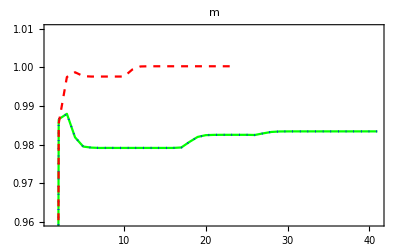

```mathematica
(*Plot Fig5*)
Fig5a1=ListLinePlot[Table[Xi01[[1]][[j1]][[1]],{j1,1,Length[Xi01[[1]]]}],PlotRange->All,PlotStyle->{Green},Frame->True];
Fig5a2=ListLinePlot[Table[Xi02[[1]][[j1]][[1]],{j1,1,Length[Xi02[[1]]]}],PlotRange->All,PlotStyle->{Blue,Dotted},Frame->True];
Fig5a3=ListLinePlot[Table[Xi03[[1]][[j1]][[1]],{j1,1,Length[Xi03[[1]]]}],PlotRange->All,PlotStyle->{Red,Dashed},Frame->True];
Fig5a=Show[Fig5a1,Fig5a2,Fig5a3,PlotRange->{0.96,1.01},PlotLabel->"m"]
```

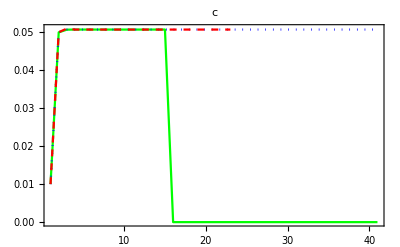

```mathematica
Fig5b1=ListLinePlot[Table[Xi01[[1]][[j1]][[2]],{j1,1,Length[Xi01[[1]]]}],PlotRange->All,PlotStyle->{Green},Frame->True];
Fig5b2=ListLinePlot[Table[Xi02[[1]][[j1]][[2]],{j1,1,Length[Xi02[[1]]]}],PlotRange->All,PlotStyle->{Blue,Dotted},Frame->True];
Fig5b3=ListLinePlot[Table[Xi03[[1]][[j1]][[2]],{j1,1,Length[Xi03[[1]]]}],PlotRange->All,PlotStyle->{Red,Dashed},Frame->True];
Fig5b=Show[Fig5b1,Fig5b2,Fig5b3,PlotRange->All,PlotLabel->"c"]
```

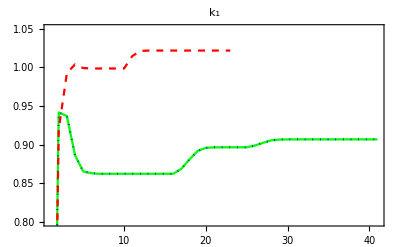

```mathematica
Fig5c1=ListLinePlot[Table[Xi01[[1]][[j1]][[3]],{j1,1,Length[Xi01[[1]]]}],PlotRange->All,PlotStyle->{Green},Frame->True];
Fig5c2=ListLinePlot[Table[Xi02[[1]][[j1]][[3]],{j1,1,Length[Xi02[[1]]]}],PlotRange->All,PlotStyle->{Blue,Dotted},Frame->True];
Fig5c3=ListLinePlot[Table[Xi03[[1]][[j1]][[3]],{j1,1,Length[Xi03[[1]]]}],PlotRange->All,PlotStyle->{Red,Dashed},Frame->True];
Fig5c=Show[Fig5c1,Fig5c2,Fig5c3,PlotRange->{0.80,1.05},PlotLabel->"k_1"]
```

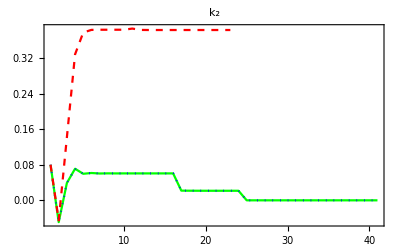

```mathematica
Fig5d1=ListLinePlot[Table[Xi01[[1]][[j1]][[4]],{j1,1,Length[Xi01[[1]]]}],PlotRange->All,PlotStyle->{Green},Frame->True];
Fig5d2=ListLinePlot[Table[Xi02[[1]][[j1]][[4]],{j1,1,Length[Xi02[[1]]]}],PlotRange->All,PlotStyle->{Blue,Dotted},Frame->True];
Fig5d3=ListLinePlot[Table[Xi03[[1]][[j1]][[4]],{j1,1,Length[Xi03[[1]]]}],PlotRange->All,PlotStyle->{Red,Dashed},Frame->True];
Fig5d=Show[Fig5d1,Fig5d2,Fig5d3,PlotRange->All,PlotLabel->"k_2"]
```

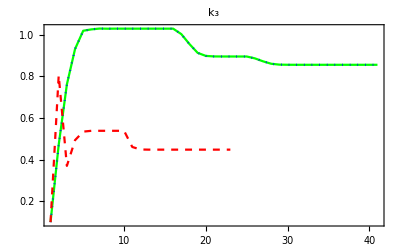

```mathematica
Fig5e1=ListLinePlot[Table[Xi01[[1]][[j1]][[5]],{j1,1,Length[Xi01[[1]]]}],PlotRange->All,PlotStyle->{Green},Frame->True];
Fig5e2=ListLinePlot[Table[Xi02[[1]][[j1]][[5]],{j1,1,Length[Xi02[[1]]]}],PlotRange->All,PlotStyle->{Blue,Dotted},Frame->True];
Fig5e3=ListLinePlot[Table[Xi03[[1]][[j1]][[5]],{j1,1,Length[Xi03[[1]]]}],PlotRange->All,PlotStyle->{Red,Dashed},Frame->True];
Fig5e=Show[Fig5e1,Fig5e2,Fig5e3,PlotRange->All,PlotLabel->"k_3"]
```

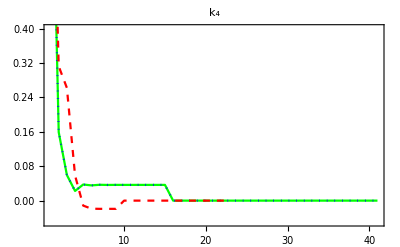

```mathematica
Fig5f1=ListLinePlot[Table[Xi01[[1]][[j1]][[6]],{j1,1,Length[Xi01[[1]]]}],PlotRange->All,PlotStyle->{Green},Frame->True];
Fig5f2=ListLinePlot[Table[Xi02[[1]][[j1]][[6]],{j1,1,Length[Xi02[[1]]]}],PlotRange->All,PlotStyle->{Blue,Dotted},Frame->True];
Fig5f3=ListLinePlot[Table[Xi03[[1]][[j1]][[6]],{j1,1,Length[Xi03[[1]]]}],PlotRange->All,PlotStyle->{Red,Dashed},Frame->True];
Fig5f=Show[Fig5f1,Fig5f2,Fig5f3,PlotRange->{-0.05,0.4},PlotLabel->"k_4"]
```

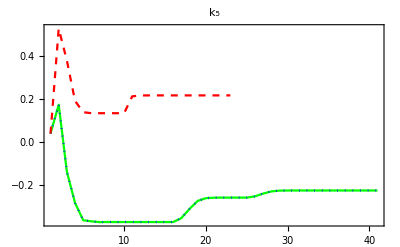

```mathematica
Fig5g1=ListLinePlot[Table[Xi01[[1]][[j1]][[7]],{j1,1,Length[Xi01[[1]]]}],PlotRange->All,PlotStyle->{Green},Frame->True];
Fig5g2=ListLinePlot[Table[Xi02[[1]][[j1]][[7]],{j1,1,Length[Xi02[[1]]]}],PlotRange->All,PlotStyle->{Blue,Dotted},Frame->True];
Fig5g3=ListLinePlot[Table[Xi03[[1]][[j1]][[7]],{j1,1,Length[Xi03[[1]]]}],PlotRange->All,PlotStyle->{Red,Dashed},Frame->True];
Fig5g=Show[Fig5g1,Fig5g2,Fig5g3,PlotRange->All,PlotLabel->"k_5"]
```

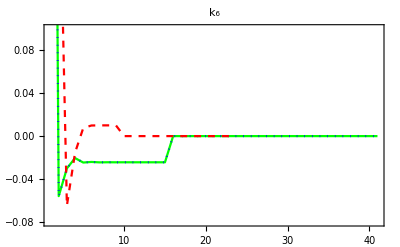

```mathematica
Fig5h1=ListLinePlot[Table[Xi01[[1]][[j1]][[8]],{j1,1,Length[Xi01[[1]]]}],PlotRange->All,PlotStyle->{Green},Frame->True];
Fig5h2=ListLinePlot[Table[Xi02[[1]][[j1]][[8]],{j1,1,Length[Xi02[[1]]]}],PlotRange->All,PlotStyle->{Blue,Dotted},Frame->True];
Fig5h3=ListLinePlot[Table[Xi03[[1]][[j1]][[8]],{j1,1,Length[Xi03[[1]]]}],PlotRange->All,PlotStyle->{Red,Dashed},Frame->True];
Fig5h=Show[Fig5h1,Fig5h2,Fig5h3,PlotRange->{-0.08,0.1},PlotLabel->"k_6"]
```

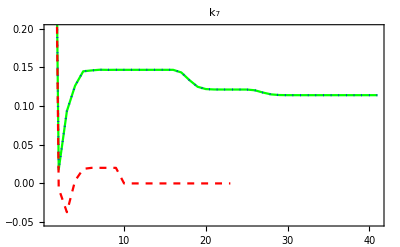

```mathematica
Fig5i1=ListLinePlot[Table[Xi01[[1]][[j1]][[9]],{j1,1,Length[Xi01[[1]]]}],PlotRange->All,PlotStyle->{Green},Frame->True];
Fig5i2=ListLinePlot[Table[Xi02[[1]][[j1]][[9]],{j1,1,Length[Xi02[[1]]]}],PlotRange->All,PlotStyle->{Blue,Dotted},Frame->True];
Fig5i3=ListLinePlot[Table[Xi03[[1]][[j1]][[9]],{j1,1,Length[Xi03[[1]]]}],PlotRange->All,PlotStyle->{Red,Dashed},Frame->True];
Fig5i=Show[Fig5i1,Fig5i2,Fig5i3,PlotRange->{-0.05,0.20},PlotLabel->"k_7"]
```

```mathematica
Fig5={Fig5a,Fig5b,Fig5c,Fig5d,Fig5e,Fig5f,Fig5g,Fig5h,Fig5i}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}